```mathematica
ssubs0={g->980,σ->20,qx->0,qy->2*Pi/3,μ->0.005,ρ->1,h0->0.1,ω->0.5*ωd};
ssubs1={g->980,σ->20,qx->0,qy->2*Pi/3*0.95,μ->0.005,ρ->1,h0->0.1,ω->0.5*ωd};
hsubs1={g->980,σ->20,qx->0,qy->2*Pi/1.5*0.95,μ->0.005,ρ->1,h0->0.1,ω->0.000001*ωd};
ssubs2={g->980,σ->20,qx->0,qy->2*Pi/3*1.05,μ->0.005,ρ->1,h0->0.1,ω->0.5*ωd};
hsubs2={g->980,σ->20,qx->0,qy->2*Pi/1.5*1.05,μ->0.005,ρ->1,h0->0.1,ω->0.000001*ωd};

Ω1[l1_]:=((qx^2+qy^2)+I*ρ/μ*(ω+l1*ωd))^(1/2)
κ=(qx^2+qy^2)^(1/2);
mat1flat[l1_,l2_]:={{2 ⅇ^(-h0 Ω1[l1]) (Cosh[h0 Ω1[l1]]+(2 (qy^2-κ^2) Cosh[h0 κ])/(κ^2+Ω1[l1]^2)),-(4 ⅇ^(-h0 Ω1[l1]) qx qy Cosh[h0 κ])/(κ^2+Ω1[l1]^2),-1/(2 κ μ ρ (κ^2+Ω1[l1]^2))ⅈ ⅇ^(-h0 (κ+Ω1[l1])) qx (2 ⅇ^(h0 (κ+Ω1[l1])) κ (ρ (g ρ+κ^2 σ) Cosh[h0 κ]+κ^3 μ^2 Sinh[h0 κ])-4 (-ⅇ^(h0 κ)+ⅇ^(h0 Ω1[l1])+ⅇ^(h0 (2 κ+Ω1[l1]))) κ^3 μ^2 Ω1[l1]+2 ⅇ^(h0 Ω1[l1]) (-1+ⅇ^(2 h0 κ)) κ^2 μ^2 Ω1[l1]^2+4 ⅇ^(h0 κ) κ μ^2 Ω1[l1]^3+ⅇ^(h0 Ω1[l1]) (-1+ⅇ^(2 h0 κ)) μ^2 Ω1[l1]^4)},{-(4 ⅇ^(-h0 Ω1[l1]) qx qy Cosh[h0 κ])/(κ^2+Ω1[l1]^2),2 ⅇ^(-h0 Ω1[l1]) (Cosh[h0 Ω1[l1]]-(2 qy^2 Cosh[h0 κ])/(κ^2+Ω1[l1]^2)),-1/(2 κ μ ρ (κ^2+Ω1[l1]^2))ⅈ ⅇ^(-h0 (κ+Ω1[l1])) qy (2 ⅇ^(h0 (κ+Ω1[l1])) κ (ρ (g ρ+κ^2 σ) Cosh[h0 κ]+κ^3 μ^2 Sinh[h0 κ])-4 (-ⅇ^(h0 κ)+ⅇ^(h0 Ω1[l1])+ⅇ^(h0 (2 κ+Ω1[l1]))) κ^3 μ^2 Ω1[l1]+2 ⅇ^(h0 Ω1[l1]) (-1+ⅇ^(2 h0 κ)) κ^2 μ^2 Ω1[l1]^2+4 ⅇ^(h0 κ) κ μ^2 Ω1[l1]^3+ⅇ^(h0 Ω1[l1]) (-1+ⅇ^(2 h0 κ)) μ^2 Ω1[l1]^4)},{4 ⅈ ⅇ^(-h0 Ω1[l1]) qx (Sinh[h0 Ω1[l1]]/(2 Ω1[l1])-(κ Sinh[h0 κ])/(κ^2+Ω1[l1]^2)),4 ⅈ ⅇ^(-h0 Ω1[l1]) qy (Sinh[h0 Ω1[l1]]/(2 Ω1[l1])-(κ Sinh[h0 κ])/(κ^2+Ω1[l1]^2)),1/(2 μ ρ (κ^2+Ω1[l1]^2))ⅇ^(-h0 (κ+Ω1[l1])) (-4 ⅇ^(h0 κ) κ^4 μ^2+ⅇ^(h0 Ω1[l1]) κ (κ^3 μ^2-g ρ^2-κ^2 ρ σ)+ⅇ^(h0 (2 κ+Ω1[l1])) κ (κ^3 μ^2+g ρ^2+κ^2 ρ σ)-4 ⅇ^(h0 Ω1[l1]) (-1+ⅇ^(2 h0 κ)) κ^3 μ^2 Ω1[l1]+2 (-2 ⅇ^(h0 κ)+ⅇ^(h0 Ω1[l1])+ⅇ^(h0 (2 κ+Ω1[l1]))) κ^2 μ^2 Ω1[l1]^2+ⅇ^(h0 Ω1[l1]) (1+ⅇ^(2 h0 κ)) μ^2 Ω1[l1]^4)}}*KroneckerDelta[l1,l2]
mat2flat[l1_,l2_]:={{0,0,-(ⅈ qx ρ Cosh[h0 κ] (-1+l1,l2+1+l1,l2))/(2 μ (κ^2+Ω1[l1]^2))},{0,0,-(ⅈ qy ρ Cosh[h0 κ] (-1+l1,l2+1+l1,l2))/(2 μ (κ^2+Ω1[l1]^2))},{0,0,(κ ρ (-1+l1,l2+1+l1,l2) Sinh[h0 κ])/(2 μ (κ^2+Ω1[l1]^2))}}

mat1[n1_,n2_,m1_,m2_,l1_,l2_]:={{C2[l1,m1,m2,n1,n2]-(2 μ C1[m1,m2,n1,n2] κx[n1,m2]^2)/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]),-(2 μ C1[m1,m2,n1,n2] κx[n1,m1] κy[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]),-((ⅈ κx[n1,m1] (C1[m1,m2,n1,n2] (g ρ^2 κ1[n1,m1]+κ1[n1,m1]^3 (ρ σ-4 μ^2 √(ρ/μ) √Ω1[n1,m1,l1]))+(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) (2 μ √(ρ/μ) (C2[l1,m1,m2,n1,n2]-S2[l1,m1,m2,n1,n2]) κ1[n1,m1] √Ω1[n1,m1,l1]+S1[m1,m2,n1,n2] (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]))))/(2 (μ κ1[n1,m1]^3+ρ κ1[n1,m1] Ω1[n1,m1,l1])))},{-(2 μ C1[m1,m2,n1,n2] κx[n1,m1] κy[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]),C2[l1,m1,m2,n1,n2]-(2 μ C1[m1,m2,n1,n2] κy[n1,m1]^2)/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]),-((ⅈ κy[n1,m1] (C1[m1,m2,n1,n2] (g ρ^2 κ1[n1,m1]+κ1[n1,m1]^3 (ρ σ-4 μ^2 √(ρ/μ) √Ω1[n1,m1,l1]))+(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) (2 μ √(ρ/μ) (C2[l1,m1,m2,n1,n2]-S2[l1,m1,m2,n1,n2]) κ1[n1,m1] √Ω1[n1,m1,l1]+S1[m1,m2,n1,n2] (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]))))/(2 (μ κ1[n1,m1]^3+ρ κ1[n1,m1] Ω1[n1,m1,l1])))},{ⅈ μ κx[n1,m1] (S2[l1,m1,m2,n1,n2]/(μ √((ρ Ω1[n1,m1,l1])/μ))-(2 S1[m1,m2,n1,n2] κ1[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1])),ⅈ μ κy[n1,m1] (S2[l1,m1,m2,n1,n2]/(μ √((ρ Ω1[n1,m1,l1])/μ))-(2 S1[m1,m2,n1,n2] κ1[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1])),1/2 (C1[m1,m2,n1,n2] (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1])+κ1[n1,m1] (2 μ (-C2[l1,m1,m2,n1,n2]+S2[l1,m1,m2,n1,n2]) κ1[n1,m1]+(S1[m1,m2,n1,n2] (g ρ^2+κ1[n1,m1]^2 (ρ σ-4 μ^2 √((ρ Ω1[n1,m1,l1])/μ))))/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1])))}} l1,l2
mat2[n1_,n2_,m1_,m2_,l1_,l2_]:=-{{0,0,-(ⅈ ρ^2 C1[m1,m2,n1,n2] κ1[n1,m1] κx[n1,m1])/(2 (μ κ1[n1,m1]^3+ρ κ1[n1,m1] Ω1[n1,m1,l1]))},{0,0,-(ⅈ ρ^2 C1[m1,m2,n1,n2] κ1[n1,m1] κy[n1,m1])/(2 (μ κ1[n1,m1]^3+ρ κ1[n1,m1] Ω1[n1,m1,l1]))},{0,0,(ρ^2 S1[m1,m2,n1,n2] κ1[n1,m1])/(2 (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]))}} (-1/2 (-1+l1,l2+1+l1,l2))
```

### symbolic inversion

```mathematica
k=(kx^2+ky^2)^(1/2)
Ω=(kx^2+ky^2+I*ρ*ω/μ)^(1/2)
ux[x_,y_,z_,t_]=(Ax*Exp[Ω*z]+Bx*Exp[-Ω*z]-A/ρ*kx/ω*Exp[k*z]-B/ρ*kx/ω*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
uy[x_,y_,z_,t_]=(Ay*Exp[Ω*z]+By*Exp[-Ω*z]-A/ρ*ky/ω*Exp[k*z]-B/ρ*ky/ω*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
uz[x_,y_,z_,t_]=(Az*Exp[Ω*z]+Bz*Exp[-Ω*z]+I*A/ρ*k/ω*Exp[k*z]-I*B/ρ*k/ω*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
P[x_,y_,z_,t_]=-ρ*g*z+(A*Exp[k*z]+B*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
h[x_,y_,z_,t_]=h0+H*Exp[I*(kx*x+ky*y+ω*t)]
subs1={A->KroneckerDelta[k1,1]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],B->KroneckerDelta[k1,2]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Ax->KroneckerDelta[k1,3]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Bx->KroneckerDelta[k1,4]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Ay->KroneckerDelta[k1,5]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],By->KroneckerDelta[k1,6]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Az->KroneckerDelta[k1,7]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Bz->KroneckerDelta[k1,8]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2], H->KroneckerDelta[k1,9]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2]};
subs2={kx->qx+n1*q1.{1,0}+m1*q2.{1,0},ky->qy+n1*q1.{0,1}+m1*q2.{0,1},ω->ω+l1*ωd};
```

√(kx^2+ky^2)

√(kx^2+ky^2+(ⅈ ρ ω)/μ)

ⅇ^(ⅈ (kx x+ky y+t ω)) (Bx ⅇ^(-z √(kx^2+ky^2+(ⅈ ρ ω)/μ))+Ax ⅇ^(z √(kx^2+ky^2+(ⅈ ρ ω)/μ))-(B ⅇ^(-√(kx^2+ky^2) z) kx)/(ρ ω)-(A ⅇ^(√(kx^2+ky^2) z) kx)/(ρ ω))

ⅇ^(ⅈ (kx x+ky y+t ω)) (By ⅇ^(-z √(kx^2+ky^2+(ⅈ ρ ω)/μ))+Ay ⅇ^(z √(kx^2+ky^2+(ⅈ ρ ω)/μ))-(B ⅇ^(-√(kx^2+ky^2) z) ky)/(ρ ω)-(A ⅇ^(√(kx^2+ky^2) z) ky)/(ρ ω))

ⅇ^(ⅈ (kx x+ky y+t ω)) (Bz ⅇ^(-z √(kx^2+ky^2+(ⅈ ρ ω)/μ))+Az ⅇ^(z √(kx^2+ky^2+(ⅈ ρ ω)/μ))-(ⅈ B ⅇ^(-√(kx^2+ky^2) z) √(kx^2+ky^2))/(ρ ω)+(ⅈ A ⅇ^(√(kx^2+ky^2) z) √(kx^2+ky^2))/(ρ ω))

ⅇ^(ⅈ (kx x+ky y+t ω)) (B ⅇ^(-√(kx^2+ky^2) z)+A ⅇ^(√(kx^2+ky^2) z))-g z ρ

ⅇ^(ⅈ (kx x+ky y+t ω)) H+h0

```mathematica
Expand[D[ux[x,y,z,t],t]-μ/ρ*(D[ux[x,y,z,t],{x,2}]+D[ux[x,y,z,t],{y,2}]+D[ux[x,y,z,t],{z,2}])+D[P[x,y,z,t],x]/ρ]
Expand[D[uy[x,y,z,t],t]-μ/ρ*(D[uy[x,y,z,t],{x,2}]+D[uy[x,y,z,t],{y,2}]+D[uy[x,y,z,t],{z,2}])+D[P[x,y,z,t],y]/ρ]
Expand[D[uz[x,y,z,t],t]-μ/ρ*(D[uz[x,y,z,t],{x,2}]+D[uz[x,y,z,t],{y,2}]+D[uz[x,y,z,t],{z,2}])+D[P[x,y,z,t],z]/ρ+g]
```

0

0

0

```mathematica
eqs1=Transpose[Table[{Simplify[Coefficient[Expand[D[ux[x,y,z,t],x]+D[uy[x,y,z,t],y]+D[uz[x,y,z,t],z]],ⅇ^(ⅈ (kx x+ky y+t ω)+z Ω)]/.subs1/.subs2],Simplify[Coefficient[Expand[D[ux[x,y,z,t],x]+D[uy[x,y,z,t],y]+D[uz[x,y,z,t],z]],ⅇ^(ⅈ (kx x+ky y+t ω)-z Ω)]/.subs1/.subs2],(I*kx*uz[x,y,z,t]*Exp[-I*(kx*x+ky*y+ω*t)]+(Exp[-I*(kx*x+ky*y+ω*t)]*D[ux[x,y,z,t],z]/.z->h0))/.z->h0/.subs1/.subs2,(I*ky*uz[x,y,z,t]*Exp[-I*(kx*x+ky*y+ω*t)]+(Exp[-I*(kx*x+ky*y+ω*t)]*D[uy[x,y,z,t],z]/.z->h0))/.z->h0/.subs1/.subs2,Simplify[(I*ω*(h[x,y,z,t]-h0)-uz[x,y,z,t]/.z->h0)*Exp[-I*(kx*x+ky*y+ω*t)]/.subs1/.subs2],Expand[(-ρ*g*(h[x,y,z,t]-h0)+(P[x,y,h0,t]+ρ*g*h0)-2*μ*(D[uz[x,y,z,t],z]/.z->h0)-σ*k^2*(h[x,y,z,t]-h0))*Exp[-I*(kx*x+ky*y+ω*t)]/.subs1/.subs2],Simplify[KroneckerDelta[l1,l2]*((KroneckerDelta[k1,3]*I2p[l1,m1,m2,n1,n2]+KroneckerDelta[k1,4]*I2m[l1,m1,m2,n1,n2])-kx/(ρ*ω)*(KroneckerDelta[k1,1]*I1p[m1,m2,n1,n2]+KroneckerDelta[k1,2]*I1m[m1,m2,n1,n2]))/.subs2],Simplify[KroneckerDelta[l1,l2]*((KroneckerDelta[k1,5]*I2p[l1,m1,m2,n1,n2]+KroneckerDelta[k1,6]*I2m[l1,m1,m2,n1,n2])-ky/(ρ*ω)*(KroneckerDelta[k1,1]*I1p[m1,m2,n1,n2]+KroneckerDelta[k1,2]*I1m[m1,m2,n1,n2]))/.subs2],Simplify[KroneckerDelta[l1,l2]*((KroneckerDelta[k1,7]*I2p[l1,m1,m2,n1,n2]+KroneckerDelta[k1,8]*I2m[l1,m1,m2,n1,n2])+I*k/(ρ*ω)*(KroneckerDelta[k1,1]*I1p[m1,m2,n1,n2]-KroneckerDelta[k1,2]*I1m[m1,m2,n1,n2]))/.subs2]},{k1,1,9}]];
```

```mathematica
elim=Range[6];
perts=DeleteDuplicates[Sort/@Cases[Permutations[Range[8],Length[elim]],u_/;Length[u]==Length[elim]]];
Monitor[dets=Table[Expand[Det[eqs1[[elim,perts[[i]]]]]],{i,1,Length[perts]}];,i]
lperts=DeleteDuplicates[First/@Position[dets,u_/;Abs[u]≠0.]]
ipert=lperts[[7]]
First/@subs1[[Complement[Range[9],perts[[ipert]]]]]
```

{2,3,4,5,7,8,9,10,11,12,13,14,18,19,20,21,24,25,26,27}

9

{Bx,By,H}

```mathematica
mat=FullSimplify[Expand[FullSimplify[Simplify[eqs1[[Complement[Range[9],elim],Complement[Range[9],perts[[ipert]]]]]-eqs1[[Complement[Range[9],elim],perts[[ipert]]]].Inverse[eqs1[[elim,perts[[ipert]]]]/.m2->m1/.n2->n1/.l2->l1].(eqs1[[elim,Complement[Range[9],perts[[ipert]]]]]/.m2->m1/.n2->n1/.l2->l1)/.qx->(κx-n1 q1.{1,0}-m1 q2.{1,0})/.qy->(κy-n1 q1.{0,1}-m1 q2.{0,1})/.ω->-I*μ/ρ(ρ/μ*Ω1[n1,m1,l1]-κx^2-κy^2)-l1 ωd/.κx^2->κ1[n1,m1]^2-κy^2,κ1[n1,m1]>0&&Ω1[n1,m1,l1]>0]/.κx^2->κ1[n1,m1]^2-κy^2/.κx->κx[n1,m1]/.κy->κy[n1,m1]/.l2->l1].DiagonalMatrix[{ⅇ^(h0 √((ρ Ω1[n1,m1,l1])/μ)),ⅇ^(h0 √((ρ Ω1[n1,m1,l1])/μ)),ρ}]]/.I2m[l1,m1,m2,n1,n2]->(C2[l1,m1,m2,n1,n2]+S2[l1,m1,m2,n1,n2])/2/ⅇ^(h0 √((ρ Ω1[n1,m1,l1])/μ))/.I2p[l1,m1,m2,n1,n2]->(C2[l1,m1,m2,n1,n2]-S2[l1,m1,m2,n1,n2])/2/ⅇ^(-h0 √((ρ Ω1[n1,m1,l1])/μ))/.I1m[m1,m2,n1,n2]->(C1[m1,m2,n1,n2]+S1[m1,m2,n1,n2])/2/ⅇ^(h0 κ1[n1,m1])/.I1p[m1,m2,n1,n2]->(C1[m1,m2,n1,n2]-S1[m1,m2,n1,n2])/2/ⅇ^(-h0 κ1[n1,m1])]/.-κ1[n1,m1]^2+κy[n1,m1]^2->-κx[n1,m2]^2;
MatrixForm[Total/@FullSimplify[CoefficientRules[#,{C1[m1,m2,n1,n2],C2[l1,m1,m2,n1,n2],S1[m1,m2,n1,n2],S2[l1,m1,m2,n1,n2]}]]&/@mat/.Rule[a_,b_]:>b*C1[m1,m2,n1,n2]^a[[1]]*C2[l1,m1,m2,n1,n2]^a[[2]]*S1[m1,m2,n1,n2]^a[[3]]*S2[l1,m1,m2,n1,n2]^a[[4]]]
```

(C2[l1,m1,m2,n1,n2]-(2 μ C1[m1,m2,n1,n2] κx[n1,m2]^2)/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) | -(2 μ C1[m1,m2,n1,n2] κx[n1,m1] κy[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) | -ⅈ μ √(ρ/μ) C2[l1,m1,m2,n1,n2] κx[n1,m1] √Ω1[n1,m1,l1]+ⅈ μ √(ρ/μ) S2[l1,m1,m2,n1,n2] κx[n1,m1] √Ω1[n1,m1,l1]-(ⅈ C1[m1,m2,n1,n2] κx[n1,m1] (g ρ^2+κ1[n1,m1]^2 (ρ σ-4 μ^2 √(ρ/μ) √Ω1[n1,m1,l1])))/(2 (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]))-(ⅈ S1[m1,m2,n1,n2] κx[n1,m1] (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]))/(2 κ1[n1,m1])
-(2 μ C1[m1,m2,n1,n2] κx[n1,m1] κy[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) | C2[l1,m1,m2,n1,n2]-(2 μ C1[m1,m2,n1,n2] κy[n1,m1]^2)/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) | -ⅈ μ √(ρ/μ) C2[l1,m1,m2,n1,n2] κy[n1,m1] √Ω1[n1,m1,l1]+ⅈ μ √(ρ/μ) S2[l1,m1,m2,n1,n2] κy[n1,m1] √Ω1[n1,m1,l1]-(ⅈ C1[m1,m2,n1,n2] κy[n1,m1] (g ρ^2+κ1[n1,m1]^2 (ρ σ-4 μ^2 √(ρ/μ) √Ω1[n1,m1,l1])))/(2 (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]))-(ⅈ S1[m1,m2,n1,n2] κy[n1,m1] (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]))/(2 κ1[n1,m1])
(ⅈ S2[l1,m1,m2,n1,n2] κx[n1,m1])/(√((ρ Ω1[n1,m1,l1])/μ))-(2 ⅈ μ S1[m1,m2,n1,n2] κ1[n1,m1] κx[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) | (ⅈ S2[l1,m1,m2,n1,n2] κy[n1,m1])/(√((ρ Ω1[n1,m1,l1])/μ))-(2 ⅈ μ S1[m1,m2,n1,n2] κ1[n1,m1] κy[n1,m1])/(μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1]) | -μ C2[l1,m1,m2,n1,n2] κ1[n1,m1]^2+μ S2[l1,m1,m2,n1,n2] κ1[n1,m1]^2+1/2 C1[m1,m2,n1,n2] (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1])+(S1[m1,m2,n1,n2] (g ρ^2 κ1[n1,m1]+κ1[n1,m1]^3 (ρ σ-4 μ^2 √((ρ Ω1[n1,m1,l1])/μ))))/(2 (μ κ1[n1,m1]^2+ρ Ω1[n1,m1,l1])))

```mathematica
FullSimplify[MatrixForm[Total/@FullSimplify[CoefficientRules[#,{C1[m1,m2,n1,n2],C2[l1,m1,m2,n1,n2],S1[m1,m2,n1,n2],S2[l1,m1,m2,n1,n2]}]]&/@mat/.Rule[a_,b_]:>b*C1[m1,m2,n1,n2]^a[[1]]*C2[l1,m1,m2,n1,n2]^a[[2]]*S1[m1,m2,n1,n2]^a[[3]]*S2[l1,m1,m2,n1,n2]^a[[4]]]/.κ[n1,m1]->Subscript[κ,m n]/.Ω1[n1,m1,l1]->Subscript["Ω",l m n]/.κx[n1,m1]->Subscript[κx,m n]/.κy[n1,m1]->Subscript[κy,m n]/.C1[m1,m2,n1,n2]->Subsuperscript[C1,m'n',m n]/.S1[m1,m2,n1,n2]->Subsuperscript[S1,m' n',m n]/.C2[l1,m1,m2,n1,n2]->Subsuperscript[C2,l'm'n',l m n]/.S2[l1,m1,m2,n1,n2]->Subsuperscript[S2,l'm'n',l m n]]
```

(C2_(l' m' n')^(l m n)-(2 μ C1_(m' n')^(m n) κx[n1,m2]^2)/(ρ Ω_(l m n)+μ κ1[n1,m1]^2) | -(2 μ κx_(m n) κy_(m n) C1_(m' n')^(m n))/(ρ Ω_(l m n)+μ κ1[n1,m1]^2) | -1/2 ⅈ κx_(m n) ((ρ Ω_(l m n) S1_(m' n')^(m n))/κ1[n1,m1]+μ S1_(m' n')^(m n) κ1[n1,m1]+(ρ C1_(m' n')^(m n) (g ρ+σ κ1[n1,m1]^2))/(ρ Ω_(l m n)+μ κ1[n1,m1]^2)+2 μ √(ρ/μ) √(Ω_(l m n)) (C2_(l' m' n')^(l m n)-S2_(l' m' n')^(l m n)-(2 μ C1_(m' n')^(m n) κ1[n1,m1]^2)/(ρ Ω_(l m n)+μ κ1[n1,m1]^2)))
-(2 μ κx_(m n) κy_(m n) C1_(m' n')^(m n))/(ρ Ω_(l m n)+μ κ1[n1,m1]^2) | C2_(l' m' n')^(l m n)-(2 μ κy_(m n)^2 C1_(m' n')^(m n))/(ρ Ω_(l m n)+μ κ1[n1,m1]^2) | -1/2 ⅈ κy_(m n) ((ρ Ω_(l m n) S1_(m' n')^(m n))/κ1[n1,m1]+μ S1_(m' n')^(m n) κ1[n1,m1]+(ρ C1_(m' n')^(m n) (g ρ+σ κ1[n1,m1]^2))/(ρ Ω_(l m n)+μ κ1[n1,m1]^2)+2 μ √(ρ/μ) √(Ω_(l m n)) (C2_(l' m' n')^(l m n)-S2_(l' m' n')^(l m n)-(2 μ C1_(m' n')^(m n) κ1[n1,m1]^2)/(ρ Ω_(l m n)+μ κ1[n1,m1]^2)))
ⅈ κx_(m n) ((S2_(l' m' n')^(l m n))/(√((ρ Ω_(l m n))/μ))-(2 μ S1_(m' n')^(m n) κ1[n1,m1])/(ρ Ω_(l m n)+μ κ1[n1,m1]^2)) | ⅈ κy_(m n) ((S2_(l' m' n')^(l m n))/(√((ρ Ω_(l m n))/μ))-(2 μ S1_(m' n')^(m n) κ1[n1,m1])/(ρ Ω_(l m n)+μ κ1[n1,m1]^2)) | 1/2 (ρ Ω_(l m n) C1_(m' n')^(m n)+κ1[n1,m1] (μ (C1_(m' n')^(m n)-2 C2_(l' m' n')^(l m n)+2 S2_(l' m' n')^(l m n)) κ1[n1,m1]+(S1_(m' n')^(m n) (g ρ^2+(ρ σ-4 μ^2 √((ρ Ω_(l m n))/μ)) κ1[n1,m1]^2))/(ρ Ω_(l m n)+μ κ1[n1,m1]^2))))

### flat substrate

```mathematica
C1[m1_,m2_,n1_,n2_]:=ⅇ^(- h0 κ1[n1,m1])*BesselI[n1-n2,1/2 as κ1[n1,m1]]*BesselI[m1-m2,1/2 as κ1[n1,m1]]+ⅇ^(h0 κ1[n1,m1])*BesselI[n1-n2,-1/2 as κ1[n1,m1]]*BesselI[m1-m2,-1/2 as κ1[n1,m1]]
```

```mathematica
M=5;
Clear[ω]
Clear[ωd]
Clear[qx]
Clear[qy]
Monitor[AbsoluteTiming[eq1base=ArrayFlatten[Table[mat1flat[l1,l2],{l1,-M,M},{l2,-M,M}]];],{l1,l2}]
Monitor[AbsoluteTiming[eq2base=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[mat2flat[l1,l2],{l1,-M,M},{l2,-M,M}]]]];],{l1,l2}]
```

{0.137556,Null}

{0.016478,Null}

```mathematica
((qx^2+qy^2)^(1/2)*Tanh[(qx^2+qy^2)^(1/2)*h0]*(g+σ/ρ*(qx^2+qy^2)))^(1/2)/(2*Pi)/.ssubs0
```

3.41953

```mathematica
freq=2*Pi*7;

{evalsbase,evecsbase}=Eigensystem[{eq1base,eq2base}/.ssubs0/.ωd->freq];
{evalsbase2,evecsbase2}=Eigensystem[{Conjugate[Transpose[eq1base]],Conjugate[Transpose[eq2base]]}/.ssubs0/.ωd->freq];
evalsbase
evalsbase2
```

{ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,209573.-1743.47 ⅈ,-209573.+1743.47 ⅈ,-98124.1+386.682 ⅈ,98124.1-386.682 ⅈ,-47547.2+8.38304 ⅈ,47547.2-8.38304 ⅈ,-15274.9+0.00104278 ⅈ,15274.9-0.00104278 ⅈ,433.884+2.15039×10^-12 ⅈ,-433.884-4.1677×10^-12 ⅈ}

{ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,2.49972×10^18+1.79243×10^17 ⅈ,-1.00272×10^18-1.52658×10^17 ⅈ,9.41962×10^17+4.43228×10^16 ⅈ,-2.25018×10^17+2.73554×10^16 ⅈ,-1.16011×10^17-1.39819×10^16 ⅈ,-209573.-1743.47 ⅈ,209573.+1743.47 ⅈ,-98124.1-386.682 ⅈ,98124.1+386.682 ⅈ,-47547.2-8.38304 ⅈ,47547.2+8.38304 ⅈ,15274.9+0.00104278 ⅈ,-15274.9-0.00104278 ⅈ,433.884+5.29929×10^-12 ⅈ,-433.884-4.82987×10^-12 ⅈ}

```mathematica
ω0=2*Pi*2;
ω1=2*Pi*10;
num=100;
freqs=Table[freq,{freq,ω0,ω1,(ω1-ω0)/num}];
AbsoluteTiming[Monitor[subharmonic=Table[Eigenvalues[{eq1base,eq2base}/.ssubs1/.ωd->freq],{freq,freqs}];,N[(freq-ω0)/(ω1-ω0)]]]
AbsoluteTiming[Monitor[harmonic=Table[Eigenvalues[{eq1base,eq2base}/.hsubs1/.ωd->freq],{freq,freqs}];,N[(freq-ω0)/(ω1-ω0)]]]
AbsoluteTiming[Monitor[subharmonic2=Table[Eigenvalues[{eq1base,eq2base}/.ssubs2/.ωd->freq],{freq,freqs}];,N[(freq-ω0)/(ω1-ω0)]]]
AbsoluteTiming[Monitor[harmonic2=Table[Eigenvalues[{eq1base,eq2base}/.hsubs2/.ωd->freq],{freq,freqs}];,N[(freq-ω0)/(ω1-ω0)]]]
```

{2.08979,Null}

{2.08893,Null}

{2.06364,Null}

{2.09859,Null}

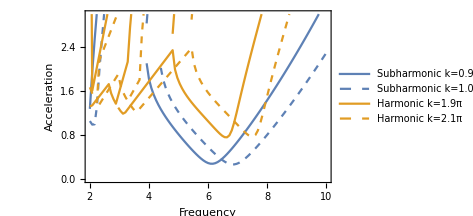

```mathematica
p=Legended[Show[ListPlot[Re[DeleteCases[Cases[#,u_/;Abs[Im[u[[2]]]]<10^-2]&/@(Transpose[{freqs/(2*Pi),#}]&/@((Transpose[SortBy[#,Re[#]&]&/@subharmonic])/980)),{}]],PlotRange->{{2,10},{0,3}},Joined->True,Axes->False,Frame->True,FrameLabel->{"Frequency","Acceleration"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotStyle->{Directive[ColorData[97,"ColorList"][[1]]]}],ListPlot[Re[DeleteCases[Cases[#,u_/;Abs[Im[u[[2]]]]<10^-2]&/@(Transpose[{freqs/(2*Pi),#}]&/@((Transpose[SortBy[#,Re[#]&]&/@subharmonic2])/980)),{}]],PlotRange->{0,3},Joined->True,Axes->False,Frame->True,FrameLabel->{"Frequency","Acceleration"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotStyle->{Directive[ColorData[97,"ColorList"][[1]],Dashed]}],ListPlot[Re[DeleteCases[Cases[#,u_/;Abs[Im[u[[2]]]]<10^-2]&/@(Transpose[{freqs/(2*Pi),#}]&/@((Transpose[SortBy[#,Re[#]&]&/@harmonic])/980)),{}]],PlotRange->{0,3},Joined->True,Axes->False,Frame->True,FrameLabel->{"Frequency","Acceleration"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotStyle->{Directive[ColorData[97,"ColorList"][[2]]]}],ListPlot[Re[DeleteCases[Cases[#,u_/;Abs[Im[u[[2]]]]<10^-2]&/@(Transpose[{freqs/(2*Pi),#}]&/@((Transpose[SortBy[#,Re[#]&]&/@harmonic2])/980)),{}]],PlotRange->{0,3},Joined->True,Axes->False,Frame->True,FrameLabel->{"Frequency","Acceleration"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotStyle->{Directive[ColorData[97,"ColorList"][[2]],Dashed]}],ImageSize->350],LineLegend[{Directive[ColorData[97,"ColorList"][[1]]],Directive[ColorData[97,"ColorList"][[1]],Dashed],Directive[ColorData[97,"ColorList"][[2]]],Directive[ColorData[97,"ColorList"][[2]],Dashed]},{"Subharmonic k=0.95π","Subharmonic k=1.05π","Harmonic k=1.9π","Harmonic k=2.1π"}]]
```

### periodic

```mathematica
S1[m1_,m2_,n1_,n2_]:=-(ⅇ^(-h0 κ1[n1,m1])*BesselI[n1-n2,1/2 as κ1[n1,m1]]*BesselI[m1-m2,1/2 as κ1[n1,m1]]-ⅇ^(h0 κ1[n1,m1])*BesselI[n1-n2,-1/2 as κ1[n1,m1]]*BesselI[m1-m2,-1/2 as κ1[n1,m1]])
C2[l1_,m1_,m2_,n1_,n2_]:=ⅇ^(-h0 √((ρ Ω1[n1,m1,l1])/μ))*BesselI[n1-n2,1/2 as √((ρ Ω1[n1,m1,l1])/μ)]*BesselI[m1-m2,1/2 as √((ρ Ω1[n1,m1,l1])/μ)]+ⅇ^(h0 √((ρ Ω1[n1,m1,l1])/μ))*BesselI[n1-n2,-1/2 as √((ρ Ω1[n1,m1,l1])/μ)]*BesselI[m1-m2,-1/2 as √((ρ Ω1[n1,m1,l1])/μ)]
S2[l1_,m1_,m2_,n1_,n2_]:=-(ⅇ^(-h0 √((ρ Ω1[n1,m1,l1])/μ))*BesselI[n1-n2,1/2 as √((ρ Ω1[n1,m1,l1])/μ)]*BesselI[m1-m2,1/2 as √((ρ Ω1[n1,m1,l1])/μ)]-ⅇ^(h0 √((ρ Ω1[n1,m1,l1])/μ))*BesselI[n1-n2,-1/2 as √((ρ Ω1[n1,m1,l1])/μ)]*BesselI[m1-m2,-1/2 as √((ρ Ω1[n1,m1,l1])/μ)])
κx[n1_,m1_]:=qx+n1*q1.{1,0}+m1*q2.{1,0}
κy[n1_,m1_]:=qy+n1*q1.{0,1}+m1*q2.{0,1}
κ1[n1_,m1_]:=(κx[n1,m1]^2+κy[n1,m1]^2)^(1/2)
Ω1[n1_,m1_,l1_]:=μ/ρ*(I*ρ/μ*(ω+l1*ωd)+κ1[n1,m1]^2)
```

```mathematica
FullSimplify[TrigToExp[((mat1[0,0,0,0,l1,l2]/.as->0)-(mat1flat[l1,l2].DiagonalMatrix[{ⅇ^(h0 √(qx^2+qy^2+(ⅈ ρ (ω+l1 ωd))/μ)),ⅇ^(h0 √(qx^2+qy^2+(ⅈ ρ (ω+l1 ωd))/μ)),ρ}]))],ρ>0&&μ>0]
FullSimplify[TrigToExp[((mat2[0,0,0,0,l1,l2]/.as->0)-(mat2flat[l1,l2].DiagonalMatrix[{ⅇ^(h0 √(qx^2+qy^2+(ⅈ ρ (ω+l1 ωd))/μ)),ⅇ^(h0 √(qx^2+qy^2+(ⅈ ρ (ω+l1 ωd))/μ)),ρ}]))],ρ>0&&μ>0]
```

{{0,0,0},{0,0,0},{0,0,0}}

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
M=5;
M2=3;
ks=2*Pi;

Monitor[AbsoluteTiming[eq1base=ArrayFlatten[Table[mat1flat[l1,l2].DiagonalMatrix[{ⅇ^(h0 √(qx^2+qy^2+(ⅈ ρ (ω+l1 ωd))/μ)),ⅇ^(h0 √(qx^2+qy^2+(ⅈ ρ (ω+l1 ωd))/μ)),ρ}],{l1,-M,M},{l2,-M,M}]];],{l1,l2}]
Monitor[AbsoluteTiming[eq2base=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[mat2flat[l1,l2].DiagonalMatrix[{ⅇ^(h0 √(qx^2+qy^2+(ⅈ ρ (ω+l1 ωd))/μ)),ⅇ^(h0 √(qx^2+qy^2+(ⅈ ρ (ω+l1 ωd))/μ)),ρ}],{l1,-M,M},{l2,-M,M}]]]];],{l1,l2}]

freq=2*Pi*7;
ks=2*Pi;
subs={q1->ks*{3.^(1/2)/2,-1/2},q2->ks*{0,1}};

{evalsbase,evecsbase}=Eigensystem[{eq1base,eq2base}/.subs/.ssubs1/.ωd->freq];
{evalsbase2,evecsbase2}=Eigensystem[{Conjugate[Transpose[eq1base]],Conjugate[Transpose[eq2base]]}/.subs/.ssubs1/.ωd->freq];

ord1=OrderingBy[evalsbase,Abs[Im[#]]&][[1;;2]];
ord2=OrderingBy[evalsbase2,Abs[Im[#]]&][[1;;2]];
ind1=ord1[[OrderingBy[evalsbase[[ord1]],Re][[-1]]]];
ind2=ord2[[OrderingBy[evalsbase2[[ord2]],Re][[-1]]]];
{evalsbase[[ind1]],evalsbase2[[ind2]]}


Monitor[AbsoluteTiming[eq1=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[Evaluate[mat1[n1,n2,m1,m2,l1,l2]/.subs/.ssubs1/.ωd->freq/.as->0.01],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]
Monitor[AbsoluteTiming[eq2=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[Evaluate[mat2[n1,n2,m1,m2,l1,l2]/.subs/.ssubs1/.ωd->freq/.as->0.01],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]

rev=Transpose[Table[Flatten[Table[KroneckerDelta[n1,0]*KroneckerDelta[m1,0]*evecsbase[[k]],{n1,-M2,M2},{m1,-M2,M2}]],{k,1,Length[evecsbase]}]];
lev=Transpose[Table[Flatten[Table[KroneckerDelta[n1,0]*KroneckerDelta[m1,0]*evecsbase2[[k]],{n1,-M2,M2},{m1,-M2,M2}]],{k,1,Length[evecsbase2]}]];

w=lev[[All,ind1]];
v=rev[[All,ind2]];
(Conjugate[w].eq1.v)/(Conjugate[w].eq2.v)
```

{0.14042,Null}

{0.022408,Null}

{671.254+4.32065×10^-13 ⅈ,671.254+2.60377×10^-9 ⅈ}

{723.074,Null}

{103.466,Null}

671.254-3.99496×10^-10 ⅈ

```mathematica
ws={};
vs={};
λs={};
w=lev[[All,ind1]];
v=rev[[All,ind2]];
AbsoluteTiming[Do[AppendTo[ws,w]; AppendTo[vs,v]; AppendTo[λs,λ];
λ=Conjugate[w].eq1.v/(Conjugate[w].eq2.v);
Print[k, " ", λ," ", Norm[eq1.v-λ*eq2.v]," ", Norm[Conjugate[Transpose[eq1]].w-Conjugate[λ*Transpose[eq2]].w]];
v=Quiet[LinearSolve[(λ*eq2-eq1),eq2.v]];
w=Quiet[LinearSolve[Conjugate[Transpose[(λ*eq2-eq1)]],Conjugate[Transpose[eq2]].w]];
v=v/Norm[v];
w=w/Norm[w];
,{k,1,10}]]
```

1 671.254-3.99496×10^-10 ⅈ 34.7368 1.27239

2 680.787-7.00982×10^-9 ⅈ 0.0953383 0.00535291

3 680.787-7.19626×10^-9 ⅈ 7.85645×10^-9 6.39919×10^-10

4 680.787-7.19621×10^-9 ⅈ 7.17363×10^-14 7.69814×10^-15

5 680.787-7.19609×10^-9 ⅈ 4.08531×10^-14 5.40697×10^-15

6 680.787-7.19623×10^-9 ⅈ 4.50472×10^-14 5.1102×10^-15

7 680.787-7.19621×10^-9 ⅈ 3.19111×10^-14 6.53878×10^-15

8 680.787-7.19638×10^-9 ⅈ 5.96839×10^-14 6.43529×10^-15

9 680.787-7.19592×10^-9 ⅈ 4.28724×10^-14 7.95318×10^-15

10 680.787-7.19626×10^-9 ⅈ 3.78425×10^-14 7.0533×10^-15

{26.8643,Null}

### continuation

```mathematica
asmax=0.03;
das=0.01;
freqmin=2*Pi*2;
freqmax=2*Pi*10;
freq0=2*Pi*7;
dfreq=2*Pi;
```

#### subharmonic

```mathematica
{evalsbase,evecsbase}=Eigensystem[{eq1base,eq2base}/.subs/.ssubs1/.ωd->freq0];
{evalsbase2,evecsbase2}=Eigensystem[{Conjugate[Transpose[eq1base]],Conjugate[Transpose[eq2base]]}/.subs/.ssubs1/.ωd->freq0];

ord1=OrderingBy[evalsbase,Abs[Im[#]]&][[1;;2]];
ord2=OrderingBy[evalsbase2,Abs[Im[#]]&][[1;;2]];
ind1=ord1[[OrderingBy[evalsbase[[ord1]],Re][[-1]]]];
ind2=ord2[[OrderingBy[evalsbase2[[ord2]],Re][[-1]]]];
{evalsbase[[ind1]],evalsbase2[[ind2]]}
rev=Transpose[Table[Flatten[Table[KroneckerDelta[n1,0]*KroneckerDelta[m1,0]*evecsbase[[k]],{n1,-M2,M2},{m1,-M2,M2}]],{k,1,Length[evecsbase]}]];
lev=Transpose[Table[Flatten[Table[KroneckerDelta[n1,0]*KroneckerDelta[m1,0]*evecsbase2[[k]],{n1,-M2,M2},{m1,-M2,M2}]],{k,1,Length[evecsbase2]}]];
```

{671.254+4.32065×10^-13 ⅈ,671.254+2.60377×10^-9 ⅈ}

```mathematica
Monitor[AbsoluteTiming[eq1=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[Evaluate[mat1[n1,n2,m1,m2,l1,l2]/.subs/.ssubs1],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]
Monitor[AbsoluteTiming[eq2=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[Evaluate[mat2[n1,n2,m1,m2,l1,l2]/.subs/.ssubs1],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]
```

{449.861,Null}

{60.3691,Null}

```mathematica
(* Quasistatically increase as *)
ws={};
vs={};
λs={};
w=lev[[All,ind1]];
v=rev[[All,ind2]];
Do[
subs2={ωd->freq0,as->As};
Print[AbsoluteTiming[test1=(eq1/.subs2);],AbsoluteTiming[test2=(eq2/.subs2);]];
AbsoluteTiming[Do[AppendTo[ws,w]; AppendTo[vs,v]; AppendTo[λs,λ];
λ=Conjugate[w].test1.v/(Conjugate[w].test2.v);
Print[k, " ", λ," ", Norm[test1.v-λ*test2.v]," ", Norm[Conjugate[Transpose[test1]].w-Conjugate[λ*Transpose[test2]].w]];
v=Quiet[LinearSolve[(λ*test2-test1),test2.v]];
w=Quiet[LinearSolve[Conjugate[Transpose[(λ*test2-test1)]],Conjugate[Transpose[test2]].w]];
v=v/Norm[v];
w=w/Norm[w];
,{k,1,10}]]
,{As,das,asmax,das}]
```

{32.2,Null}{4.84504,Null}

1 671.254-3.99467×10^-10 ⅈ 34.7368 1.27239

2 680.787-7.00982×10^-9 ⅈ 0.0953383 0.00535291

3 680.787-7.19635×10^-9 ⅈ 7.85645×10^-9 6.39919×10^-10

4 680.787-7.19615×10^-9 ⅈ 4.8874×10^-14 7.254×10^-15

5 680.787-7.19581×10^-9 ⅈ 5.25887×10^-14 7.90858×10^-15

6 680.787-7.19629×10^-9 ⅈ 3.70546×10^-14 7.80619×10^-15

7 680.787-7.19632×10^-9 ⅈ 6.24929×10^-14 6.52111×10^-15

8 680.787-7.19626×10^-9 ⅈ 4.07649×10^-14 7.80248×10^-15

9 680.787-7.19646×10^-9 ⅈ 6.96502×10^-14 9.21177×10^-15

10 680.787-7.19638×10^-9 ⅈ 5.24139×10^-14 6.37519×10^-15

{31.279,Null}{4.7078,Null}

1 700.1-2.09026×10^-8 ⅈ 33.3691 1.30942

2 710.216-4.04228×10^-8 ⅈ 0.075651 0.00569214

3 710.216-4.07931×10^-8 ⅈ 4.24824×10^-9 4.88775×10^-10

4 710.216-4.07932×10^-8 ⅈ 1.00464×10^-13 2.38564×10^-14

5 710.216-4.07932×10^-8 ⅈ 1.06116×10^-13 2.21306×10^-14

6 710.216-4.07929×10^-8 ⅈ 6.47971×10^-14 2.31972×10^-14

7 710.216-4.07928×10^-8 ⅈ 9.69457×10^-14 2.29419×10^-14

8 710.216-4.07932×10^-8 ⅈ 8.74739×10^-14 2.36133×10^-14

9 710.216-4.07925×10^-8 ⅈ 7.0305×10^-14 2.39758×10^-14

10 710.216-4.07929×10^-8 ⅈ 9.04416×10^-14 2.13343×10^-14

{32.603,Null}{4.99455,Null}

1 750.775-8.36105×10^-8 ⅈ 28.3756 1.4062

2 762.203-1.5144×10^-7 ⅈ 0.051947 0.00662972

3 762.203-1.52557×10^-7 ⅈ 1.22427×10^-9 2.57914×10^-10

4 762.203-1.52557×10^-7 ⅈ 1.4583×10^-13 1.14503×10^-13

5 762.203-1.52557×10^-7 ⅈ 1.37749×10^-13 1.18176×10^-13

6 762.203-1.52557×10^-7 ⅈ 1.37602×10^-13 1.28068×10^-13

7 762.203-1.52557×10^-7 ⅈ 1.32563×10^-13 1.22569×10^-13

8 762.203-1.52557×10^-7 ⅈ 1.32583×10^-13 1.22517×10^-13

9 762.203-1.52557×10^-7 ⅈ 1.44644×10^-13 1.19788×10^-13

10 762.203-1.52557×10^-7 ⅈ 1.52262×10^-13 1.31501×10^-13

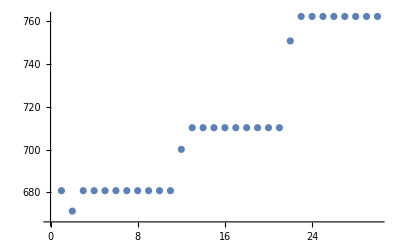

```mathematica
ListPlot[Re[λs]]
v0=vs[[-1]];
w0=ws[[-1]];
λ0=λs[[-1]];
```

```mathematica
w=w0;
v=v0;
λps={};
AbsoluteTiming[Do[
subs2={ωd->freq,as->asmax};
Print[AbsoluteTiming[test1=(eq1/.subs2);],AbsoluteTiming[test2=(eq2/.subs2);]];
AbsoluteTiming[Do[ AppendTo[λps,λ];
λ=Conjugate[w].test1.v/(Conjugate[w].test2.v);
Print[k, " ", λ," ", Norm[test1.v-λ*test2.v]," ", Norm[Conjugate[Transpose[test1]].w-Conjugate[λ*Transpose[test2]].w]];
v=Quiet[LinearSolve[(λ*test2-test1),test2.v]];
w=Quiet[LinearSolve[Conjugate[Transpose[(λ*test2-test1)]],Conjugate[Transpose[test2]].w]];
v=v/Norm[v];
w=w/Norm[w];
,{k,1,10}]]
,{freq,freq0,freqmax,dfreq}]]
```

{31.7284,Null}{4.84882,Null}

1 762.203-1.52557×10^-7 ⅈ 1.52262×10^-13 1.31501×10^-13

2 762.203-1.52558×10^-7 ⅈ 1.24751×10^-13 1.23916×10^-13

3 762.203-1.52557×10^-7 ⅈ 1.3865×10^-13 1.16352×10^-13

4 762.203-1.52557×10^-7 ⅈ 1.28183×10^-13 1.10046×10^-13

5 762.203-1.52557×10^-7 ⅈ 1.26736×10^-13 1.23292×10^-13

6 762.203-1.52557×10^-7 ⅈ 1.35955×10^-13 1.19453×10^-13

7 762.203-1.52557×10^-7 ⅈ 1.43851×10^-13 1.173×10^-13

8 762.203-1.52557×10^-7 ⅈ 1.6834×10^-13 1.15863×10^-13

9 762.203-1.52557×10^-7 ⅈ 1.31768×10^-13 1.23385×10^-13

10 762.203-1.52557×10^-7 ⅈ 1.29507×10^-13 1.30625×10^-13

{32.3817,Null}{4.72638,Null}

1 1487.84+1.39142×10^-6 ⅈ 23.8461 41.0485

2 1523.29-0.0000104672 ⅈ 0.117962 0.0437512

3 1523.3-0.0000103764 ⅈ 3.47549×10^-7 8.93096×10^-8

4 1523.3-0.0000103764 ⅈ 2.76312×10^-13 6.78836×10^-13

5 1523.3-0.0000103764 ⅈ 2.99512×10^-13 7.09162×10^-13

6 1523.3-0.0000103764 ⅈ 2.70451×10^-13 7.01193×10^-13

7 1523.3-0.0000103764 ⅈ 2.83202×10^-13 7.05973×10^-13

8 1523.3-0.0000103764 ⅈ 2.87576×10^-13 7.19378×10^-13

9 1523.3-0.0000103764 ⅈ 2.62395×10^-13 7.02563×10^-13

10 1523.3-0.0000103764 ⅈ 2.76024×10^-13 6.70141×10^-13

{32.2061,Null}{4.72582,Null}

1 2377.4+0.0000384133 ⅈ 27.0099 150.686

2 2390.14-0.000244941 ⅈ 0.162562 0.0070262

3 2390.14-0.000245001 ⅈ 1.02754×10^-7 1.86631×10^-9

4 2390.14-0.000245001 ⅈ 5.68819×10^-13 4.76761×10^-12

5 2390.14-0.000245001 ⅈ 5.25998×10^-13 5.14859×10^-12

6 2390.14-0.000245001 ⅈ 5.5949×10^-13 4.84312×10^-12

7 2390.14-0.000245001 ⅈ 5.13594×10^-13 4.69294×10^-12

8 2390.14-0.000245001 ⅈ 6.73157×10^-13 4.79209×10^-12

9 2390.14-0.000245001 ⅈ 5.15464×10^-13 4.59478×10^-12

10 2390.14-0.000245001 ⅈ 4.95239×10^-13 4.77431×10^-12

{32.3898,Null}{4.68896,Null}

1 3336.67-0.00141834 ⅈ 34.5373 1160.6

2 3359.55+0.000979032 ⅈ 0.386346 0.0244451

3 3359.55+0.00096963 ⅈ 6.49926×10^-7 3.80377×10^-8

4 3359.55+0.00096963 ⅈ 1.12432×10^-12 2.35286×10^-11

5 3359.55+0.00096963 ⅈ 1.1493×10^-12 2.52252×10^-11

6 3359.55+0.00096963 ⅈ 1.19755×10^-12 2.36147×10^-11

7 3359.55+0.00096963 ⅈ 1.10694×10^-12 2.39331×10^-11

8 3359.55+0.00096963 ⅈ 1.11241×10^-12 2.35215×10^-11

9 3359.55+0.00096963 ⅈ 1.10372×10^-12 2.37868×10^-11

10 3359.55+0.00096963 ⅈ 1.20789×10^-12 2.38134×10^-11

{373.194,Null}

```mathematica
w=w0;
v=v0;
λms={};
AbsoluteTiming[Do[
subs2={ωd->freq,as->asmax};
Print[AbsoluteTiming[test1=(eq1/.subs2);],AbsoluteTiming[test2=(eq2/.subs2);]];
AbsoluteTiming[Do[ AppendTo[λms,λ];
λ=Conjugate[w].test1.v/(Conjugate[w].test2.v);
Print[k, " ", λ," ", Norm[test1.v-λ*test2.v]," ", Norm[Conjugate[Transpose[test1]].w-Conjugate[λ*Transpose[test2]].w]];
v=Quiet[LinearSolve[(λ*test2-test1),test2.v]];
w=Quiet[LinearSolve[Conjugate[Transpose[(λ*test2-test1)]],Conjugate[Transpose[test2]].w]];
v=v/Norm[v];
w=w/Norm[w];
,{k,1,10}]]
,{freq,freq0,freqmin,-dfreq}]]
```

{31.8579,Null}{4.72794,Null}

1 762.203-1.52557×10^-7 ⅈ 1.52262×10^-13 1.31501×10^-13

2 762.203-1.52558×10^-7 ⅈ 1.24751×10^-13 1.23916×10^-13

3 762.203-1.52557×10^-7 ⅈ 1.3865×10^-13 1.16352×10^-13

4 762.203-1.52557×10^-7 ⅈ 1.28183×10^-13 1.10046×10^-13

5 762.203-1.52557×10^-7 ⅈ 1.26736×10^-13 1.23292×10^-13

6 762.203-1.52557×10^-7 ⅈ 1.35955×10^-13 1.19453×10^-13

7 762.203-1.52557×10^-7 ⅈ 1.43851×10^-13 1.173×10^-13

8 762.203-1.52557×10^-7 ⅈ 1.6834×10^-13 1.15863×10^-13

9 762.203-1.52557×10^-7 ⅈ 1.31768×10^-13 1.23385×10^-13

10 762.203-1.52557×10^-7 ⅈ 1.29507×10^-13 1.30625×10^-13

{31.7857,Null}{4.67872,Null}

1 108.209-1.49073×10^-6 ⅈ 18.6613 7.10155

2 239.926-1.01426×10^-6 ⅈ 2.35978 2.24759

3 295.87-4.1159×10^-8 ⅈ 0.268996 0.26379

4 296.567-3.63727×10^-11 ⅈ 0.000317576 0.00031229

5 296.567-3.62448×10^-11 ⅈ 5.22416×10^-13 5.08125×10^-13

6 296.567-3.6195×10^-11 ⅈ 9.85979×10^-14 6.17592×10^-15

7 296.567-3.60885×10^-11 ⅈ 8.41385×10^-14 6.58263×10^-15

8 296.567-3.60103×10^-11 ⅈ 1.11496×10^-13 7.43903×10^-15

9 296.567-3.61595×10^-11 ⅈ 9.81109×10^-14 8.22679×10^-15

10 296.567-3.62377×10^-11 ⅈ 9.99956×10^-14 7.17829×10^-15

{31.6876,Null}{4.71408,Null}

1 324.482+1.0381×10^-10 ⅈ 20.7546 7.16196

2 666.264-5.09335×10^-7 ⅈ 3.88956 4.98762

3 753.06-4.76689×10^-6 ⅈ 0.251988 0.336911

4 753.41-4.72141×10^-6 ⅈ 0.0000591875 0.0000793628

5 753.41-4.72141×10^-6 ⅈ 7.24681×10^-14 3.01741×10^-14

6 753.41-4.72141×10^-6 ⅈ 7.59462×10^-14 3.14695×10^-14

7 753.41-4.72141×10^-6 ⅈ 6.92125×10^-14 2.96671×10^-14

8 753.41-4.72141×10^-6 ⅈ 6.88099×10^-14 3.17362×10^-14

9 753.41-4.72141×10^-6 ⅈ 7.83898×10^-14 3.20372×10^-14

10 753.41-4.72141×10^-6 ⅈ 7.58071×10^-14 3.04082×10^-14

{31.4325,Null}{4.70713,Null}

1 1338.31+0.0000525521 ⅈ 12.9536 12.9034

2 1636.92-0.019484 ⅈ 0.585206 2.31699

3 1658.45-0.141301 ⅈ 0.0551763 0.244548

4 1658.76-0.14556 ⅈ 0.0000916566 0.000404644

5 1658.76-0.14556 ⅈ 4.35385×10^-13 1.90413×10^-12

6 1658.76-0.14556 ⅈ 7.91062×10^-14 4.33427×10^-13

7 1658.76-0.14556 ⅈ 9.57564×10^-14 3.92744×10^-13

8 1658.76-0.14556 ⅈ 9.56458×10^-14 4.31873×10^-13

9 1658.76-0.14556 ⅈ 1.17469×10^-13 4.26213×10^-13

10 1658.76-0.14556 ⅈ 8.73879×10^-14 5.25388×10^-13

{31.0101,Null}{4.68797,Null}

1 3278.99-2.46303 ⅈ 18.2974 45.7932

2 937.442+254.071 ⅈ 9.4388 57.1303

3 192.826+626.022 ⅈ 13.1273 30.159

4 1585.47+1432.82 ⅈ 14.9953 23.3702

5 1305.74+1407.99 ⅈ 1.06202 7.37381

6 1320.87+1399.29 ⅈ 0.0191454 0.175758

7 1320.86+1399.3 ⅈ 4.55172×10^-7 3.9378×10^-6

8 1320.86+1399.3 ⅈ 6.0697×10^-14 6.37803×10^-14

9 1320.86+1399.3 ⅈ 6.02294×10^-14 5.43024×10^-14

10 1320.86+1399.3 ⅈ 6.65428×10^-14 5.50008×10^-14

{30.7757,Null}{4.70579,Null}

1 328.103+1433.71 ⅈ 21.8811 21.5551

2 528.801+416.304 ⅈ 5.86337 8.75213

3 677.675+853.542 ⅈ 3.86433 4.24461

4 679.179+804.912 ⅈ 0.133071 0.144171

5 679.168+804.984 ⅈ 4.76872×10^-6 5.48221×10^-6

6 679.168+804.984 ⅈ 4.72708×10^-14 1.45814×10^-14

7 679.168+804.984 ⅈ 4.30887×10^-14 2.67143×10^-14

8 679.168+804.984 ⅈ 3.74569×10^-14 1.20242×10^-14

9 679.168+804.984 ⅈ 6.49922×10^-14 1.28782×10^-14

10 679.168+804.984 ⅈ 5.11233×10^-14 1.30642×10^-14

{554.503,Null}

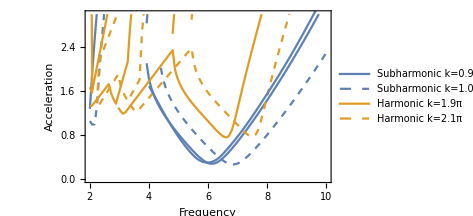

```mathematica
Show[p,ListPlot[{#[[1]],Abs[Re[#[[2]]]]}&/@Join[Reverse[Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmin,-dfreq}],λms[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-1]][[1;;-2]],Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmax,dfreq}],λps[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-2]],Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]]],InterpolationOrder->2]]
```

#### subharmonic2

```mathematica
{evalsbase,evecsbase}=Eigensystem[{eq1base,eq2base}/.subs/.ssubs2/.ωd->freq0];
{evalsbase2,evecsbase2}=Eigensystem[{Conjugate[Transpose[eq1base]],Conjugate[Transpose[eq2base]]}/.subs/.ssubs2/.ωd->freq0];
ord1=OrderingBy[evalsbase,Abs[Im[#]]&][[1;;2]];
ord2=OrderingBy[evalsbase2,Abs[Im[#]]&][[1;;2]];
ind1=ord1[[OrderingBy[evalsbase[[ord1]],Re][[-1]]]];
ind2=ord2[[OrderingBy[evalsbase2[[ord2]],Re][[-1]]]];
{evalsbase[[ind1]],evalsbase2[[ind2]]}

rev=Transpose[Table[Flatten[Table[KroneckerDelta[n1,0]*KroneckerDelta[m1,0]*evecsbase[[k]],{n1,-M2,M2},{m1,-M2,M2}]],{k,1,Length[evecsbase]}]];
lev=Transpose[Table[Flatten[Table[KroneckerDelta[n1,0]*KroneckerDelta[m1,0]*evecsbase2[[k]],{n1,-M2,M2},{m1,-M2,M2}]],{k,1,Length[evecsbase2]}]];
```

{280.841+1.35242×10^-13 ⅈ,280.841+4.0396×10^-10 ⅈ}

```mathematica
Monitor[AbsoluteTiming[eq1=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[Evaluate[mat1[n1,n2,m1,m2,l1,l2]/.subs/.ssubs2],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]
Monitor[AbsoluteTiming[eq2=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[Evaluate[mat2[n1,n2,m1,m2,l1,l2]/.subs/.ssubs2],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]
```

{408.318,Null}

{57.0901,Null}

```mathematica
(* Quasistatically increase as *)
ws={};
vs={};
λs={};
w=lev[[All,ind1]];
v=rev[[All,ind2]];
Do[
subs2={ωd->freq0,as->As};
Print[AbsoluteTiming[test1=(eq1/.subs2);],AbsoluteTiming[test2=(eq2/.subs2);]];
AbsoluteTiming[Do[AppendTo[ws,w]; AppendTo[vs,v]; AppendTo[λs,λ];
λ=Conjugate[w].test1.v/(Conjugate[w].test2.v);
Print[k, " ", λ," ", Norm[test1.v-λ*test2.v]," ", Norm[Conjugate[Transpose[test1]].w-Conjugate[λ*Transpose[test2]].w]];
v=Quiet[LinearSolve[(λ*test2-test1),test2.v]];
w=Quiet[LinearSolve[Conjugate[Transpose[(λ*test2-test1)]],Conjugate[Transpose[test2]].w]];
v=v/Norm[v];
w=w/Norm[w];
,{k,1,10}]]
,{As,das,asmax,das}]
```

{30.1137,Null}{4.75092,Null}

1 280.841-1.19471×10^-10 ⅈ 33.9257 1.25512

2 285.848-6.53699×10^-13 ⅈ 0.0528983 0.00326914

3 285.848-3.83693×10^-13 ⅈ 4.17604×10^-9 3.48473×10^-10

4 285.848-4.54747×10^-13 ⅈ 4.55071×10^-14 3.48342×10^-15

5 285.848-3.97904×10^-13 ⅈ 4.07218×10^-14 3.35267×10^-15

6 285.848-5.40012×10^-13 ⅈ 5.41463×10^-14 4.94022×10^-15

7 285.848-4.90274×10^-13 ⅈ 3.72796×10^-14 6.0696×10^-15

8 285.848-4.36984×10^-13 ⅈ 3.86969×10^-14 5.76173×10^-15

9 285.848-3.97904×10^-13 ⅈ 5.17802×10^-14 3.58284×10^-15

10 285.848-5.11591×10^-13 ⅈ 4.27496×10^-14 2.93857×10^-15

{30.9072,Null}{4.74543,Null}

1 296.166-1.86517×10^-12 ⅈ 32.8075 1.27951

2 302.342-3.28981×10^-12 ⅈ 0.0491427 0.00497137

3 302.342-3.5314×10^-12 ⅈ 9.0574×10^-9 1.24727×10^-9

4 302.342-3.43903×10^-12 ⅈ 7.88804×10^-14 6.24346×10^-15

5 302.342-3.4035×10^-12 ⅈ 8.95687×10^-14 5.18144×10^-15

6 302.342-3.24007×10^-12 ⅈ 8.06335×10^-14 7.90959×10^-15

7 302.342-3.41061×10^-12 ⅈ 7.46114×10^-14 7.32819×10^-15

8 302.342-3.46745×10^-12 ⅈ 9.31642×10^-14 4.96212×10^-15

9 302.342-3.38218×10^-12 ⅈ 9.60781×10^-14 5.24163×10^-15

10 302.342-3.24007×10^-12 ⅈ 9.06687×10^-14 9.33116×10^-15

{31.818,Null}{4.74814,Null}

1 326.082-1.25056×10^-11 ⅈ 28.1589 1.35585

2 334.719-2.49543×10^-11 ⅈ 0.0417151 0.00850771

3 334.719-2.48406×10^-11 ⅈ 1.85107×10^-8 5.39991×10^-9

4 334.719-2.50964×10^-11 ⅈ 1.41575×10^-13 1.36279×10^-14

5 334.719-2.48619×10^-11 ⅈ 1.20562×10^-13 1.58091×10^-14

6 334.719-2.50395×10^-11 ⅈ 1.22112×10^-13 1.40181×10^-14

7 334.719-2.49045×10^-11 ⅈ 1.25795×10^-13 1.34776×10^-14

8 334.719-2.48832×10^-11 ⅈ 1.29502×10^-13 1.73008×10^-14

9 334.719-2.51248×10^-11 ⅈ 1.27464×10^-13 1.40521×10^-14

10 334.719-2.49543×10^-11 ⅈ 1.33854×10^-13 1.33752×10^-14

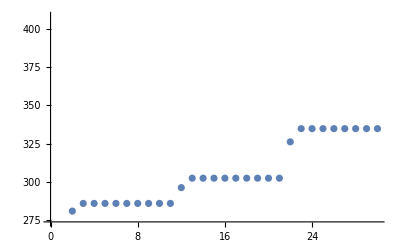

```mathematica
ListPlot[Re[λs]]
v0=vs[[-1]];
w0=ws[[-1]];
λ0=λs[[-1]];
```

```mathematica
w=w0;
v=v0;
λps2={};
AbsoluteTiming[Do[
subs2={ωd->freq,as->asmax};
Print[AbsoluteTiming[test1=(eq1/.subs2);],AbsoluteTiming[test2=(eq2/.subs2);]];
AbsoluteTiming[Do[ AppendTo[λps2,λ];
λ=Conjugate[w].test1.v/(Conjugate[w].test2.v);
Print[k, " ", λ," ", Norm[test1.v-λ*test2.v]," ", Norm[Conjugate[Transpose[test1]].w-Conjugate[λ*Transpose[test2]].w]];
v=Quiet[LinearSolve[(λ*test2-test1),test2.v]];
w=Quiet[LinearSolve[Conjugate[Transpose[(λ*test2-test1)]],Conjugate[Transpose[test2]].w]];
v=v/Norm[v];
w=w/Norm[w];
,{k,1,10}]]
,{freq,freq0,freqmax,dfreq}]]
```

{31.38,Null}{4.703,Null}

1 334.719-2.49543×10^-11 ⅈ 1.33854×10^-13 1.33752×10^-14

2 334.719-2.49827×10^-11 ⅈ 1.27342×10^-13 1.3814×10^-14

3 334.719-2.50537×10^-11 ⅈ 1.4024×10^-13 1.27773×10^-14

4 334.719-2.50502×10^-11 ⅈ 1.17478×10^-13 1.43013×10^-14

5 334.719-2.50111×10^-11 ⅈ 1.27984×10^-13 1.38137×10^-14

6 334.719-2.50395×10^-11 ⅈ 1.25287×10^-13 1.40162×10^-14

7 334.719-2.49543×10^-11 ⅈ 1.35605×10^-13 1.37684×10^-14

8 334.719-2.51248×10^-11 ⅈ 1.25843×10^-13 1.30439×10^-14

9 334.719-2.49116×10^-11 ⅈ 1.3483×10^-13 1.40719×10^-14

10 334.719-2.50111×10^-11 ⅈ 1.31233×10^-13 1.34739×10^-14

{31.8437,Null}{4.70997,Null}

1 690.331-3.8753×10^-10 ⅈ 26.8139 6.40036

2 887.071-2.14027×10^-8 ⅈ 1.56654 1.00321

3 890.726-3.73314×10^-8 ⅈ 0.00303477 0.00204817

4 890.726-3.73301×10^-8 ⅈ 2.7264×10^-11 1.7966×10^-11

5 890.726-3.73299×10^-8 ⅈ 2.19197×10^-13 1.9271×10^-13

6 890.726-3.73302×10^-8 ⅈ 2.08049×10^-13 1.91855×10^-13

7 890.726-3.73302×10^-8 ⅈ 2.29805×10^-13 1.94864×10^-13

8 890.726-3.73299×10^-8 ⅈ 2.02151×10^-13 2.01595×10^-13

9 890.726-3.73298×10^-8 ⅈ 2.18355×10^-13 1.97689×10^-13

10 890.726-3.73307×10^-8 ⅈ 2.19545×10^-13 1.90281×10^-13

{31.7938,Null}{4.73865,Null}

1 1580.64+2.67846×10^-7 ⅈ 27.4311 50.2765

2 1600.53-2.72285×10^-6 ⅈ 0.129664 0.0185252

3 1600.53-2.72216×10^-6 ⅈ 8.98755×10^-8 6.4908×10^-9

4 1600.53-2.72216×10^-6 ⅈ 4.04601×10^-13 1.09335×10^-12

5 1600.53-2.72216×10^-6 ⅈ 4.24195×10^-13 1.06599×10^-12

6 1600.53-2.72216×10^-6 ⅈ 4.34578×10^-13 1.1625×10^-12

7 1600.53-2.72216×10^-6 ⅈ 4.10973×10^-13 1.03796×10^-12

8 1600.53-2.72216×10^-6 ⅈ 3.97637×10^-13 1.07305×10^-12

9 1600.53-2.72216×10^-6 ⅈ 3.81379×10^-13 1.10926×10^-12

10 1600.53-2.72216×10^-6 ⅈ 3.9932×10^-13 1.02617×10^-12

{32.0899,Null}{4.75582,Null}

1 2379.58-3.06677×10^-6 ⅈ 30.8671 227.8

2 2399.32-5.43151×10^-6 ⅈ 0.406147 0.025954

3 2399.33-5.78896×10^-6 ⅈ 7.61108×10^-6 1.6299×10^-7

4 2399.33-5.78896×10^-6 ⅈ 8.82867×10^-13 9.03177×10^-12

5 2399.33-5.78896×10^-6 ⅈ 8.45801×10^-13 8.44801×10^-12

6 2399.33-5.78896×10^-6 ⅈ 9.49321×10^-13 8.78581×10^-12

7 2399.33-5.78896×10^-6 ⅈ 9.52708×10^-13 8.32726×10^-12

8 2399.33-5.78896×10^-6 ⅈ 8.74564×10^-13 8.52129×10^-12

9 2399.33-5.78896×10^-6 ⅈ 9.42703×10^-13 8.76992×10^-12

10 2399.33-5.78896×10^-6 ⅈ 9.51988×10^-13 7.91052×10^-12

{381.145,Null}

```mathematica
w=w0;
v=v0;
λms2={};
AbsoluteTiming[Do[
subs2={ωd->freq,as->asmax};
Print[AbsoluteTiming[test1=(eq1/.subs2);],AbsoluteTiming[test2=(eq2/.subs2);]];
AbsoluteTiming[Do[ AppendTo[λms2,λ];
λ=Conjugate[w].test1.v/(Conjugate[w].test2.v);
Print[k, " ", λ," ", Norm[test1.v-λ*test2.v]," ", Norm[Conjugate[Transpose[test1]].w-Conjugate[λ*Transpose[test2]].w]];
v=Quiet[LinearSolve[(λ*test2-test1),test2.v]];
w=Quiet[LinearSolve[Conjugate[Transpose[(λ*test2-test1)]],Conjugate[Transpose[test2]].w]];
v=v/Norm[v];
w=w/Norm[w];
,{k,1,10}]]
,{freq,freq0,freqmin,-dfreq}]]
```

{31.5437,Null}{4.71381,Null}

1 334.719-2.49543×10^-11 ⅈ 1.33854×10^-13 1.33752×10^-14

2 334.719-2.49827×10^-11 ⅈ 1.27342×10^-13 1.3814×10^-14

3 334.719-2.50537×10^-11 ⅈ 1.4024×10^-13 1.27773×10^-14

4 334.719-2.50502×10^-11 ⅈ 1.17478×10^-13 1.43013×10^-14

5 334.719-2.50111×10^-11 ⅈ 1.27984×10^-13 1.38137×10^-14

6 334.719-2.50395×10^-11 ⅈ 1.25287×10^-13 1.40162×10^-14

7 334.719-2.49543×10^-11 ⅈ 1.35605×10^-13 1.37684×10^-14

8 334.719-2.51248×10^-11 ⅈ 1.25843×10^-13 1.30439×10^-14

9 334.719-2.49116×10^-11 ⅈ 1.3483×10^-13 1.40719×10^-14

10 334.719-2.50111×10^-11 ⅈ 1.31233×10^-13 1.34739×10^-14

{31.7003,Null}{4.72533,Null}

1 13.0939+3.03231×10^-10 ⅈ 23.6667 6.27692

2 33.1604+1.23198×10^-9 ⅈ 7.73735 7.99061

3 98.4314+6.21127×10^-9 ⅈ 7.58673 8.07648

4 270.435+1.66044×10^-8 ⅈ 6.64013 7.08127

5 493.07+1.21585×10^-8 ⅈ 2.73214 2.91628

6 527.023+4.29681×10^-9 ⅈ 0.0940689 0.100446

7 527.062+4.27252×10^-9 ⅈ 3.47953×10^-6 3.71585×10^-6

8 527.062+4.27271×10^-9 ⅈ 1.02605×10^-13 1.93979×10^-14

9 527.062+4.27297×10^-9 ⅈ 1.02316×10^-13 1.862×10^-14

10 527.062+4.27274×10^-9 ⅈ 9.10186×10^-14 1.82705×10^-14

{31.3666,Null}{4.75544,Null}

1 1007.69+7.06612×10^-8 ⅈ 15.2201 9.98049

2 1133.76-3.06415×10^-6 ⅈ 0.254497 0.427537

3 1134.-0.0000153625 ⅈ 0.0000272612 0.0000513736

4 1134.-0.0000153625 ⅈ 1.01264×10^-13 1.13644×10^-13

5 1134.-0.0000153625 ⅈ 8.66686×10^-14 1.20781×10^-13

6 1134.-0.0000153625 ⅈ 9.11813×10^-14 1.12946×10^-13

7 1134.-0.0000153625 ⅈ 9.16557×10^-14 1.16373×10^-13

8 1134.-0.0000153625 ⅈ 9.4185×10^-14 1.09572×10^-13

9 1134.-0.0000153625 ⅈ 9.12155×10^-14 1.14475×10^-13

10 1134.-0.0000153625 ⅈ 9.36101×10^-14 1.1204×10^-13

{31.3925,Null}{4.71002,Null}

1 1809.17+0.00017875 ⅈ 14.0436 19.9595

2 1119.55-19.6504 ⅈ 11.5312 16.7109

3 3648.67-28.7009 ⅈ 32.0108 43.6838

4 1810.08-64.036 ⅈ 9.71516 11.7678

5 1859.28+163.117 ⅈ 11.6386 19.6024

6 1957.63-68.5255 ⅈ 7.0828 3.27115

7 1981.64-56.6056 ⅈ 1.98749 1.37623

8 1973.08-66.8247 ⅈ 0.578332 0.350593

9 1972.04-68.5392 ⅈ 0.0561034 0.0320769

10 1972.04-68.5596 ⅈ 0.0000663331 0.0000379533

{30.9233,Null}{4.73477,Null}

1 2613.04+142.635 ⅈ 72.0305 306.953

2 2637.76-11.2483 ⅈ 5.18255 10.3506

3 2617.24+6.08006 ⅈ 0.192305 0.362896

4 2617.26+6.08512 ⅈ 0.0000528807 0.0000684152

5 2617.26+6.08512 ⅈ 7.59866×10^-13 2.2043×10^-12

6 2617.26+6.08512 ⅈ 3.14413×10^-13 2.27652×10^-12

7 2617.26+6.08512 ⅈ 3.70764×10^-13 2.73588×10^-12

8 2617.26+6.08512 ⅈ 3.36709×10^-13 2.44909×10^-12

9 2617.26+6.08512 ⅈ 3.44935×10^-13 2.35266×10^-12

10 2617.26+6.08512 ⅈ 3.33134×10^-13 2.71831×10^-12

{30.6121,Null}{4.75209,Null}

1 3555.6-30.1212 ⅈ 62.6233 138.141

2 3494.78+10.4806 ⅈ 1.4407 4.37283

3 3495.51+8.45639 ⅈ 0.00816784 0.0236762

4 3495.51+8.47412 ⅈ 0.0000227757 0.0000749473

5 3495.51+8.47411 ⅈ 1.31508×10^-12 4.32422×10^-12

6 3495.51+8.47411 ⅈ 1.13847×10^-13 3.82356×10^-13

7 3495.51+8.47411 ⅈ 1.2814×10^-13 4.16281×10^-13

8 3495.51+8.47411 ⅈ 1.53299×10^-13 3.87765×10^-13

9 3495.51+8.47411 ⅈ 1.38459×10^-13 4.27934×10^-13

10 3495.51+8.47411 ⅈ 1.32132×10^-13 3.45994×10^-13

{570.903,Null}

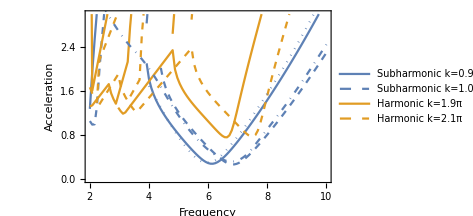

```mathematica
Show[p,ListPlot[{#[[1]],Abs[Re[#[[2]]]]}&/@Join[Reverse[Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmin,-dfreq}],λms2[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-1]][[1;;-2]],Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmax,dfreq}],λps2[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-2]],Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],DotDashed],InterpolationOrder->2],ListPlot[{#[[1]],Abs[Re[#[[2]]]]}&/@Join[Reverse[Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmin,-dfreq}],λms[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-1]][[1;;-2]],Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmax,dfreq}],λps[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-2]],Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],Dotted],InterpolationOrder->2]]
```

#### harmonic

```mathematica
{evalsbase,evecsbase}=Eigensystem[{eq1base,eq2base}/.subs/.hsubs1/.ωd->freq0];
{evalsbase2,evecsbase2}=Eigensystem[{Conjugate[Transpose[eq1base]],Conjugate[Transpose[eq2base]]}/.subs/.hsubs1/.ωd->freq0];
ord1=OrderingBy[evalsbase,Abs[#]&][[1;;4]];
ord2=OrderingBy[evalsbase2,Abs[#]&][[1;;4]];
ind1=ord1[[OrderingBy[evalsbase[[ord1]],Re][[-1]]]];
ind2=ord2[[OrderingBy[evalsbase2[[ord2]],Re][[-1]]]];
{evalsbase[[ind1]],evalsbase2[[ind2]]}

rev=Transpose[Table[Flatten[Table[KroneckerDelta[n1,0]*KroneckerDelta[m1,0]*evecsbase[[k]],{n1,-M2,M2},{m1,-M2,M2}]],{k,1,Length[evecsbase]}]];
lev=Transpose[Table[Flatten[Table[KroneckerDelta[n1,0]*KroneckerDelta[m1,0]*evecsbase2[[k]],{n1,-M2,M2},{m1,-M2,M2}]],{k,1,Length[evecsbase2]}]];
```

{1265.28+0.00541987 ⅈ,1265.28-0.00541988 ⅈ}

```mathematica
Monitor[AbsoluteTiming[eq1=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[Evaluate[mat1[n1,n2,m1,m2,l1,l2]/.subs/.hsubs1],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]
Monitor[AbsoluteTiming[eq2=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[Evaluate[mat2[n1,n2,m1,m2,l1,l2]/.subs/.hsubs1],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]
```

{406.274,Null}

{56.9028,Null}

```mathematica
(* Quasistatically increase as *)
ws={};
vs={};
λs={};
w=lev[[All,ind1]];
v=rev[[All,ind2]];
Do[
subs2={ωd->freq0,as->As};
Print[AbsoluteTiming[test1=(eq1/.subs2);],AbsoluteTiming[test2=(eq2/.subs2);]];
AbsoluteTiming[Do[AppendTo[ws,w]; AppendTo[vs,v]; AppendTo[λs,λ];
λ=Conjugate[w].test1.v/(Conjugate[w].test2.v);
Print[k, " ", λ," ", Norm[test1.v-λ*test2.v]," ", Norm[Conjugate[Transpose[test1]].w-Conjugate[λ*Transpose[test2]].w]];
v=Quiet[LinearSolve[(λ*test2-test1),test2.v]];
w=Quiet[LinearSolve[Conjugate[Transpose[(λ*test2-test1)]],Conjugate[Transpose[test2]].w]];
v=v/Norm[v];
w=w/Norm[w];
,{k,1,10}]]
,{As,das,asmax,das}]
```

{29.9366,Null}{4.73868,Null}

1 -1265.28-0.00541988 ⅈ 149.995 4.30096

2 -1310.13+0.0467168 ⅈ 0.0000115467 0.184022

3 -1310.12+0.0466431 ⅈ 6.91467×10^-11 1.79185×10^-6

4 -1310.12+0.0466431 ⅈ 2.06375×10^-16 3.50523×10^-10

5 -1310.12+0.0466431 ⅈ 1.93244×10^-16 4.86737×10^-10

6 -1310.12+0.0466431 ⅈ 2.85049×10^-16 4.36981×10^-10

7 -1310.12+0.0466431 ⅈ 1.57955×10^-16 3.3743×10^-10

8 -1310.12+0.0466431 ⅈ 2.91705×10^-16 2.18518×10^-10

9 -1310.12+0.0466431 ⅈ 1.66299×10^-16 3.03144×10^-10

10 -1310.12+0.0466431 ⅈ 1.21308×10^-16 2.60508×10^-10

{30.9063,Null}{4.71251,Null}

1 -1468.78+0.494506 ⅈ 0.0281376 13.7839

2 -1318.85+0.103332 ⅈ 0.0000551029 3.33986

3 -1312.31+0.0576426 ⅈ 3.25131×10^-7 0.0321673

4 -1312.31+0.057631 ⅈ 2.90336×10^-13 2.84312×10^-8

5 -1312.31+0.057631 ⅈ 7.27544×10^-16 9.49389×10^-10

6 -1312.31+0.057631 ⅈ 8.01311×10^-16 1.06491×10^-9

7 -1312.31+0.057631 ⅈ 9.2092×10^-16 2.65915×10^-9

8 -1312.31+0.057631 ⅈ 8.49592×10^-16 4.33868×10^-9

9 -1312.31+0.057631 ⅈ 8.64368×10^-16 2.27309×10^-9

10 -1312.31+0.057631 ⅈ 7.48594×10^-16 1.76839×10^-9

{31.3534,Null}{4.71672,Null}

1 -1418.26-0.0419626 ⅈ 0.00816876 9.85378

2 -1411.99+0.0380869 ⅈ 4.86898×10^-7 0.0250837

3 -1411.99+0.0380721 ⅈ 3.90136×10^-13 4.155×10^-8

4 -1411.99+0.0380721 ⅈ 9.77475×10^-16 1.4172×10^-8

5 -1411.99+0.0380721 ⅈ 1.35226×10^-15 2.80733×10^-8

6 -1411.99+0.0380721 ⅈ 1.26198×10^-15 1.67891×10^-8

7 -1411.99+0.0380721 ⅈ 1.30382×10^-15 3.60074×10^-8

8 -1411.99+0.0380721 ⅈ 1.07396×10^-15 3.12405×10^-8

9 -1411.99+0.0380721 ⅈ 9.86488×10^-16 1.7135×10^-8

10 -1411.99+0.0380721 ⅈ 1.01725×10^-15 1.88084×10^-8

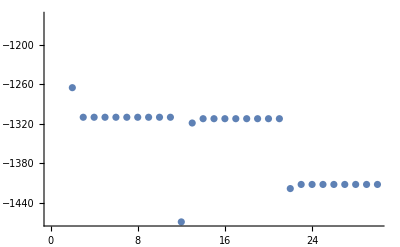

```mathematica
ListPlot[Re[λs]]
v0=vs[[-1]];
w0=ws[[-1]];
λ0=λs[[-1]];
```

```mathematica
w=w0;
v=v0;
λph1={};
AbsoluteTiming[Do[
subs2={ωd->freq,as->asmax};
Print[AbsoluteTiming[test1=(eq1/.subs2);],AbsoluteTiming[test2=(eq2/.subs2);]];
AbsoluteTiming[Do[ AppendTo[λph1,λ];
λ=Conjugate[w].test1.v/(Conjugate[w].test2.v);
Print[k, " ", λ," ", Norm[test1.v-λ*test2.v]," ", Norm[Conjugate[Transpose[test1]].w-Conjugate[λ*Transpose[test2]].w]];
v=Quiet[LinearSolve[(λ*test2-test1),test2.v]];
w=Quiet[LinearSolve[Conjugate[Transpose[(λ*test2-test1)]],Conjugate[Transpose[test2]].w]];
v=v/Norm[v];
w=w/Norm[w];
,{k,1,10}]]
,{freq,freq0,freqmax,dfreq}]]
```

{31.4844,Null}{4.71256,Null}

1 -1411.99+0.0380721 ⅈ 1.01725×10^-15 1.88084×10^-8

2 -1411.99+0.0380721 ⅈ 9.61483×10^-16 3.28452×10^-8

3 -1411.99+0.0380721 ⅈ 1.08288×10^-15 3.54502×10^-8

4 -1411.99+0.0380721 ⅈ 1.24263×10^-15 1.66832×10^-8

5 -1411.99+0.0380721 ⅈ 1.02284×10^-15 2.98366×10^-8

6 -1411.99+0.0380721 ⅈ 1.04773×10^-15 4.10303×10^-8

7 -1411.99+0.0380721 ⅈ 1.01768×10^-15 1.6066×10^-8

8 -1411.99+0.0380721 ⅈ 9.31374×10^-16 1.54066×10^-8

9 -1411.99+0.0380721 ⅈ 1.02361×10^-15 9.08404×10^-9

10 -1411.99+0.0380721 ⅈ 1.10777×10^-15 1.30387×10^-8

{31.7799,Null}{4.72375,Null}

1 -3714.49+0.138733 ⅈ 0.000338848 1356.06

2 -3504.77-0.000712133 ⅈ 0.000113028 2.51682

3 -3506.47+0.000119475 ⅈ 1.03056×10^-7 0.00441152

4 -3506.47+0.000119472 ⅈ 1.11828×10^-15 1.68838×10^-8

5 -3506.47+0.000119472 ⅈ 8.88676×10^-16 4.42091×10^-9

6 -3506.47+0.000119472 ⅈ 8.87602×10^-16 9.54581×10^-9

7 -3506.47+0.000119472 ⅈ 1.05657×10^-15 7.88596×10^-9

8 -3506.47+0.000119472 ⅈ 8.62825×10^-16 1.41177×10^-8

9 -3506.47+0.000119472 ⅈ 9.27903×10^-16 2.11791×10^-8

10 -3506.47+0.000119472 ⅈ 8.67155×10^-16 5.8736×10^-9

{31.7398,Null}{4.73818,Null}

1 -5547.16+0.00409829 ⅈ 0.000491129 42950.4

2 -5487.18-0.000260153 ⅈ 0.000012499 0.572547

3 -5486.9+0.000063525 ⅈ 1.78885×10^-9 0.002517

4 -5486.9+0.0000635512 ⅈ 1.3119×10^-15 7.49227×10^-8

5 -5486.9+0.0000635512 ⅈ 1.16245×10^-15 2.10989×10^-8

6 -5486.9+0.0000635512 ⅈ 1.30639×10^-15 2.11278×10^-8

7 -5486.9+0.0000635512 ⅈ 1.18327×10^-15 2.98053×10^-8

8 -5486.9+0.0000635512 ⅈ 1.23281×10^-15 2.67432×10^-8

9 -5486.9+0.0000635512 ⅈ 1.04594×10^-15 6.55839×10^-8

10 -5486.9+0.0000635512 ⅈ 1.07716×10^-15 4.13498×10^-8

{31.9492,Null}{4.72689,Null}

1 -7600.07-0.00142371 ⅈ 0.000379727 75418.4

2 -7592.81+0.000572291 ⅈ 7.24283×10^-7 0.0192835

3 -7592.81+0.000572238 ⅈ 6.05469×10^-14 5.01592×10^-8

4 -7592.81+0.000572238 ⅈ 1.07699×10^-15 1.49121×10^-7

5 -7592.81+0.000572238 ⅈ 9.79227×10^-16 1.4351×10^-7

6 -7592.81+0.000572238 ⅈ 8.96417×10^-16 9.74063×10^-8

7 -7592.81+0.000572238 ⅈ 9.18733×10^-16 5.98009×10^-8

8 -7592.81+0.000572238 ⅈ 8.84296×10^-16 3.76925×10^-8

9 -7592.81+0.000572238 ⅈ 1.26349×10^-15 1.31132×10^-7

10 -7592.81+0.000572238 ⅈ 1.13251×10^-15 1.11126×10^-7

{379.522,Null}

```mathematica
w=w0;
v=v0;
λmh1={};
AbsoluteTiming[Do[
subs2={ωd->freq,as->asmax};
Print[AbsoluteTiming[test1=(eq1/.subs2);],AbsoluteTiming[test2=(eq2/.subs2);]];
AbsoluteTiming[Do[ AppendTo[λmh1,λ];
λ=Conjugate[w].test1.v/(Conjugate[w].test2.v);
Print[k, " ", λ," ", Norm[test1.v-λ*test2.v]," ", Norm[Conjugate[Transpose[test1]].w-Conjugate[λ*Transpose[test2]].w]];
v=Quiet[LinearSolve[(λ*test2-test1),test2.v]];
w=Quiet[LinearSolve[Conjugate[Transpose[(λ*test2-test1)]],Conjugate[Transpose[test2]].w]];
v=v/Norm[v];
w=w/Norm[w];
,{k,1,10}]]
,{freq,freq0,freqmin,-dfreq}]]
```

{31.6613,Null}{4.71682,Null}

1 -1411.99+0.0380721 ⅈ 1.01725×10^-15 1.88084×10^-8

2 -1411.99+0.0380721 ⅈ 9.61483×10^-16 3.28452×10^-8

3 -1411.99+0.0380721 ⅈ 1.08288×10^-15 3.54502×10^-8

4 -1411.99+0.0380721 ⅈ 1.24263×10^-15 1.66832×10^-8

5 -1411.99+0.0380721 ⅈ 1.02284×10^-15 2.98366×10^-8

6 -1411.99+0.0380721 ⅈ 1.04773×10^-15 4.10303×10^-8

7 -1411.99+0.0380721 ⅈ 1.01768×10^-15 1.6066×10^-8

8 -1411.99+0.0380721 ⅈ 9.31374×10^-16 1.54066×10^-8

9 -1411.99+0.0380721 ⅈ 1.02361×10^-15 9.08404×10^-9

10 -1411.99+0.0380721 ⅈ 1.10777×10^-15 1.30387×10^-8

{31.3352,Null}{4.74958,Null}

1 700.288-0.0847756 ⅈ 0.00031274 146.638

2 992.489-0.306245 ⅈ 0.000148251 27.1886

3 767.772-0.0864848 ⅈ 8.50018×10^-6 2.26622

4 769.252-0.0907354 ⅈ 1.00123×10^-8 0.00269245

5 769.252-0.0907354 ⅈ 1.11911×10^-15 4.52352×10^-9

6 769.252-0.0907354 ⅈ 1.18376×10^-15 6.0957×10^-9

7 769.252-0.0907354 ⅈ 1.21088×10^-15 8.16751×10^-9

8 769.252-0.0907354 ⅈ 1.53184×10^-15 6.03271×10^-9

9 769.252-0.0907354 ⅈ 1.049×10^-15 5.25273×10^-9

10 769.252-0.0907354 ⅈ 1.20467×10^-15 8.94255×10^-10

{31.1772,Null}{4.73764,Null}

1 1195.67-0.163919 ⅈ 0.000125872 33.0225

2 1243.64-0.140921 ⅈ 2.89988×10^-6 1.08164

3 1243.04-0.141493 ⅈ 1.9381×10^-9 0.00101213

4 1243.04-0.141493 ⅈ 1.07249×10^-15 7.06853×10^-9

5 1243.04-0.141493 ⅈ 1.40263×10^-15 9.10729×10^-9

6 1243.04-0.141493 ⅈ 1.01042×10^-15 6.02958×10^-9

7 1243.04-0.141493 ⅈ 2.27491×10^-15 9.56083×10^-9

8 1243.04-0.141493 ⅈ 1.39651×10^-15 1.45355×10^-8

9 1243.04-0.141493 ⅈ 1.33877×10^-15 6.12471×10^-9

10 1243.04-0.141493 ⅈ 3.85929×10^-15 6.2543×10^-9

{31.1064,Null}{4.75726,Null}

1 1449.42-0.564635 ⅈ 0.0000806028 110.78

2 1500.29-0.17229 ⅈ 0.000092296 14.4393

3 1642.18-0.0669807 ⅈ 0.0000116739 4.604

4 1638.15-0.0824576 ⅈ 6.7714×10^-8 0.0170674

5 1638.15-0.0824574 ⅈ 1.51193×10^-15 2.25681×10^-8

6 1638.15-0.0824574 ⅈ 1.27129×10^-15 3.36139×10^-9

7 1638.15-0.0824574 ⅈ 1.13043×10^-15 2.59554×10^-8

8 1638.15-0.0824574 ⅈ 1.25597×10^-15 1.22748×10^-7

9 1638.15-0.0824574 ⅈ 9.26821×10^-16 1.93443×10^-8

10 1638.15-0.0824574 ⅈ 1.76615×10^-15 5.25161×10^-8

{30.935,Null}{4.72679,Null}

1 2772.09-0.154427 ⅈ 0.000209885 101.251

2 2423.75-0.167462 ⅈ 0.000146292 30.6802

3 2637.9-0.185771 ⅈ 0.000176655 25.0635

4 2212.82-2011.62 ⅈ 0.000488084 149.943

5 2519.91-671.359 ⅈ 0.000163829 50.0566

6 2618.91-223.023 ⅈ 0.0000559277 16.8095

7 2649.39-72.9056 ⅈ 0.0000186573 5.61822

8 2659.95-25.0008 ⅈ 7.00528×10^-6 1.82727

9 2663.88-10.1328 ⅈ 2.26224×10^-6 0.532029

10 2665.23-7.36987 ⅈ 3.05378×10^-7 0.0779201

{30.6234,Null}{4.73958,Null}

1 3438.9-531.475 ⅈ 0.000305595 136.174

2 3364.31+29.6734 ⅈ 0.0000569673 38.9812

3 3375.66+53.0279 ⅈ 5.31968×10^-6 8.1282

4 3379.87-3.02142 ⅈ 1.73906×10^-6 1.94981

5 3371.83-0.0561079 ⅈ 9.60914×10^-8 0.191822

6 3371.81-0.00854006 ⅈ 9.54619×10^-11 0.0000820553

7 3371.81-0.00854007 ⅈ 1.19345×10^-15 3.42052×10^-7

8 3371.81-0.00854007 ⅈ 3.13759×10^-15 5.55788×10^-7

9 3371.81-0.00854007 ⅈ 2.90838×10^-15 6.43611×10^-7

10 3371.81-0.00854007 ⅈ 4.98234×10^-15 1.70345×10^-7

{567.393,Null}

```mathematica
Show[p,ListPlot[{#[[1]],Abs[Re[#[[2]]]]}&/@Join[Reverse[Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmin,-dfreq}],λmh2[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-1]][[1;;-2]],Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmax,dfreq}],λph2[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-2]],Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[2]],Dotted],InterpolationOrder->2],ListPlot[{#[[1]],Abs[Re[#[[2]]]]}&/@Join[Reverse[Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmin,-dfreq}],λms2[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-1]][[1;;-2]],Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmax,dfreq}],λps2[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-2]],Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],DotDashed],InterpolationOrder->2],ListPlot[{#[[1]],Abs[Re[#[[2]]]]}&/@Join[Reverse[Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmin,-dfreq}],λms[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-1]][[1;;-2]],Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmax,dfreq}],λps[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-2]],Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],Dotted],InterpolationOrder->2]]
```

Part::take: Cannot take positions 10 through -1 in λmh2.

Transpose::nmtx: The first two levels of {{7,6,5,4,3,2},1/980 λmh2⟦10;;-1;;10⟧} cannot be transposed.

Part::take: Cannot take positions 1 through -2 in {}.

Part::take: Cannot take positions 10 through -1 in λph2.

General::stop: Further output of Part::take will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{7,8,9,10},1/980 λph2⟦10;;-1;;10⟧} cannot be transposed.

Join::heads: Heads Part and List at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

-Graphics-

#### harmonic2

```mathematica
{evalsbase,evecsbase}=Eigensystem[{eq1base,eq2base}/.subs/.hsubs2/.ωd->freq0];
{evalsbase2,evecsbase2}=Eigensystem[{Conjugate[Transpose[eq1base]],Conjugate[Transpose[eq2base]]}/.subs/.hsubs2/.ωd->freq0];
ord1=OrderingBy[evalsbase,Abs[#]&][[1;;4]];
ord2=OrderingBy[evalsbase2,Abs[#]&][[1;;4]];
ind1=ord1[[OrderingBy[evalsbase[[ord1]],Re][[-1]]]];
ind2=ord2[[OrderingBy[evalsbase2[[ord2]],Re][[-1]]]];
{evalsbase[[ind1]],evalsbase2[[ind2]]}

rev=Transpose[Table[Flatten[Table[KroneckerDelta[n1,0]*KroneckerDelta[m1,0]*evecsbase[[k]],{n1,-M2,M2},{m1,-M2,M2}]],{k,1,Length[evecsbase]}]];
lev=Transpose[Table[Flatten[Table[KroneckerDelta[n1,0]*KroneckerDelta[m1,0]*evecsbase2[[k]],{n1,-M2,M2},{m1,-M2,M2}]],{k,1,Length[evecsbase2]}]];
```

{966.011+0.00288813 ⅈ,966.011-0.00288813 ⅈ}

```mathematica
Monitor[AbsoluteTiming[eq1=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[Evaluate[mat1[n1,n2,m1,m2,l1,l2]/.subs/.hsubs2],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]
Monitor[AbsoluteTiming[eq2=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[Evaluate[mat2[n1,n2,m1,m2,l1,l2]/.subs/.hsubs2],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]
```

{407.821,Null}

{57.4999,Null}

```mathematica
(* Quasistatically increase as *)
ws={};
vs={};
λs={};
w=lev[[All,ind1]];
v=rev[[All,ind2]];
Do[
subs2={ωd->freq0,as->As};
Print[AbsoluteTiming[test1=(eq1/.subs2);],AbsoluteTiming[test2=(eq2/.subs2);]];
AbsoluteTiming[Do[AppendTo[ws,w]; AppendTo[vs,v]; AppendTo[λs,λ];
λ=Conjugate[w].test1.v/(Conjugate[w].test2.v);
Print[k, " ", λ," ", Norm[test1.v-λ*test2.v]," ", Norm[Conjugate[Transpose[test1]].w-Conjugate[λ*Transpose[test2]].w]];
v=Quiet[LinearSolve[(λ*test2-test1),test2.v]];
w=Quiet[LinearSolve[Conjugate[Transpose[(λ*test2-test1)]],Conjugate[Transpose[test2]].w]];
v=v/Norm[v];
w=w/Norm[w];
,{k,1,10}]]
,{As,das,asmax,das}]
```

{30.1587,Null}{4.7927,Null}

1 966.011+0.00288813 ⅈ 390.913 10.8973

2 1191.88-1.07845 ⅈ 0.0000381685 5.49452

3 1187.15-1.00214 ⅈ 1.90001×10^-7 0.0253345

4 1187.15-1.00214 ⅈ 1.24129×10^-14 1.27888×10^-8

5 1187.15-1.00214 ⅈ 2.21593×10^-16 1.21647×10^-8

6 1187.15-1.00214 ⅈ 6.13702×10^-16 1.25031×10^-8

7 1187.15-1.00214 ⅈ 8.66099×10^-16 1.98771×10^-8

8 1187.15-1.00214 ⅈ 4.5409×10^-16 1.09738×10^-8

9 1187.15-1.00214 ⅈ 8.17132×10^-16 3.94054×10^-8

10 1187.15-1.00214 ⅈ 9.65302×10^-16 1.60757×10^-8

{30.8178,Null}{4.75103,Null}

1 7018.13-89.4878 ⅈ 0.0219234 414.671

2 3237.99+322.175 ⅈ 0.00356747 112.618

3 3499.86-689.729 ⅈ 0.00143419 53.6545

4 3573.88-41.5887 ⅈ 0.000783651 42.2513

5 3653.02-0.969764 ⅈ 0.0000351926 13.704

6 3645.24-0.00397872 ⅈ 2.00728×10^-7 0.131619

7 3645.24-0.00322432 ⅈ 2.37992×10^-13 3.48051×10^-7

8 3645.24-0.00322432 ⅈ 6.77921×10^-16 8.44807×10^-8

9 3645.24-0.00322432 ⅈ 7.08388×10^-16 1.24494×10^-7

10 3645.24-0.00322432 ⅈ 6.62918×10^-16 1.12302×10^-7

{31.4184,Null}{4.76012,Null}

1 3624.3-0.00164825 ⅈ 0.0219857 17.0812

2 3617.89-0.00329262 ⅈ 2.95769×10^-7 0.0226075

3 3617.89-0.00329267 ⅈ 5.48483×10^-14 5.08946×10^-7

4 3617.89-0.00329267 ⅈ 1.08804×10^-15 4.86987×10^-7

5 3617.89-0.00329267 ⅈ 1.0517×10^-15 4.74495×10^-7

6 3617.89-0.00329267 ⅈ 1.24079×10^-15 4.79782×10^-7

7 3617.89-0.00329267 ⅈ 9.99965×10^-16 4.76004×10^-7

8 3617.89-0.00329267 ⅈ 1.24287×10^-15 9.5498×10^-7

9 3617.89-0.00329267 ⅈ 1.12991×10^-15 2.0528×10^-7

10 3617.89-0.00329267 ⅈ 1.0205×10^-15 9.83825×10^-7

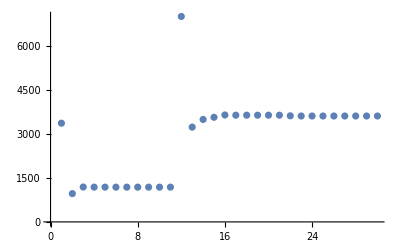

```mathematica
ListPlot[Re[λs]]
v0=vs[[-1]];
w0=ws[[-1]];
λ0=λs[[-1]];
```

```mathematica
w=w0;
v=v0;
λph2={};
AbsoluteTiming[Do[
subs2={ωd->freq,as->asmax};
Print[AbsoluteTiming[test1=(eq1/.subs2);],AbsoluteTiming[test2=(eq2/.subs2);]];
AbsoluteTiming[Do[ AppendTo[λph2,λ];
λ=Conjugate[w].test1.v/(Conjugate[w].test2.v);
Print[k, " ", λ," ", Norm[test1.v-λ*test2.v]," ", Norm[Conjugate[Transpose[test1]].w-Conjugate[λ*Transpose[test2]].w]];
v=Quiet[LinearSolve[(λ*test2-test1),test2.v]];
w=Quiet[LinearSolve[Conjugate[Transpose[(λ*test2-test1)]],Conjugate[Transpose[test2]].w]];
v=v/Norm[v];
w=w/Norm[w];
,{k,1,10}]]
,{freq,freq0,freqmax,dfreq}]]
```

{31.5747,Null}{4.76,Null}

1 3617.89-0.00329267 ⅈ 1.0205×10^-15 9.83825×10^-7

2 3617.89-0.00329267 ⅈ 1.10725×10^-15 6.23793×10^-7

3 3617.89-0.00329267 ⅈ 1.11197×10^-15 3.72706×10^-7

4 3617.89-0.00329267 ⅈ 1.21963×10^-15 8.49136×10^-7

5 3617.89-0.00329267 ⅈ 1.11244×10^-15 7.61019×10^-8

6 3617.89-0.00329267 ⅈ 1.26515×10^-15 5.53949×10^-7

7 3617.89-0.00329267 ⅈ 9.69165×10^-16 1.71572×10^-7

8 3617.89-0.00329267 ⅈ 8.07357×10^-16 7.91725×10^-7

9 3617.89-0.00329267 ⅈ 1.1501×10^-15 3.96315×10^-7

10 3617.89-0.00329267 ⅈ 1.08831×10^-15 1.57803×10^-7

{31.7771,Null}{4.74069,Null}

1 2694.98-0.0233499 ⅈ 0.000262249 327456.

2 2848.63+0.00110118 ⅈ 0.000142266 6.04388

3 2850.66+0.0018528 ⅈ 1.60768×10^-7 0.0111747

4 2850.66+0.00185281 ⅈ 2.67577×10^-15 1.46673×10^-8

5 2850.66+0.00185281 ⅈ 8.39564×10^-16 2.05857×10^-7

6 2850.66+0.00185281 ⅈ 1.34706×10^-15 2.15232×10^-7

7 2850.66+0.00185281 ⅈ 1.5507×10^-15 1.66478×10^-7

8 2850.66+0.00185281 ⅈ 9.95954×10^-16 7.84016×10^-8

9 2850.66+0.00185281 ⅈ 8.96457×10^-16 1.95536×10^-7

10 2850.66+0.00185281 ⅈ 8.97008×10^-16 2.12579×10^-7

{31.8368,Null}{4.73909,Null}

1 2181.68+0.0207815 ⅈ 0.000437084 445076.

2 -6604.21+0.745048 ⅈ 0.00276954 444.823

3 741.968-0.38533 ⅈ 0.000798742 95.0373

4 586.351-0.733538 ⅈ 0.000288116 153.552

5 684.813-2.14622 ⅈ 0.000143792 119.846

6 1085.76+0.129912 ⅈ 8.69548×10^-6 115.185

7 1071.06-0.141974 ⅈ 1.68213×10^-7 0.853568

8 1071.08-0.14112 ⅈ 1.03343×10^-11 0.000036081

9 1071.08-0.14112 ⅈ 1.50842×10^-15 1.1128×10^-7

10 1071.08-0.14112 ⅈ 1.42029×10^-15 2.82986×10^-6

{31.8369,Null}{4.76419,Null}

1 659.049-0.144308 ⅈ 0.000144208 4374.01

2 689.188-0.0976256 ⅈ 2.56213×10^-6 0.433438

3 689.155-0.0977373 ⅈ 8.0413×10^-11 0.0000103594

4 689.155-0.0977373 ⅈ 2.29583×10^-15 5.50537×10^-7

5 689.155-0.0977373 ⅈ 1.19393×10^-15 4.23295×10^-7

6 689.155-0.0977373 ⅈ 3.19406×10^-15 3.45761×10^-7

7 689.155-0.0977373 ⅈ 2.24965×10^-15 3.45299×10^-7

8 689.155-0.0977373 ⅈ 3.12487×10^-15 3.35577×10^-7

9 689.155-0.0977373 ⅈ 2.4772×10^-15 5.1104×10^-7

10 689.155-0.0977373 ⅈ 2.43321×10^-15 1.87743×10^-7

{384.034,Null}

```mathematica
w=w0;
v=v0;
λmh2={};
AbsoluteTiming[Do[
subs2={ωd->freq,as->asmax};
Print[AbsoluteTiming[test1=(eq1/.subs2);],AbsoluteTiming[test2=(eq2/.subs2);]];
AbsoluteTiming[Do[ AppendTo[λmh2,λ];
λ=Conjugate[w].test1.v/(Conjugate[w].test2.v);
Print[k, " ", λ," ", Norm[test1.v-λ*test2.v]," ", Norm[Conjugate[Transpose[test1]].w-Conjugate[λ*Transpose[test2]].w]];
v=Quiet[LinearSolve[(λ*test2-test1),test2.v]];
w=Quiet[LinearSolve[Conjugate[Transpose[(λ*test2-test1)]],Conjugate[Transpose[test2]].w]];
v=v/Norm[v];
w=w/Norm[w];
,{k,1,10}]]
,{freq,freq0,freqmin,-dfreq}]]
```

{31.5781,Null}{4.74933,Null}

1 3617.89-0.00329267 ⅈ 1.0205×10^-15 9.83825×10^-7

2 3617.89-0.00329267 ⅈ 1.10725×10^-15 6.23793×10^-7

3 3617.89-0.00329267 ⅈ 1.11197×10^-15 3.72706×10^-7

4 3617.89-0.00329267 ⅈ 1.21963×10^-15 8.49136×10^-7

5 3617.89-0.00329267 ⅈ 1.11244×10^-15 7.61019×10^-8

6 3617.89-0.00329267 ⅈ 1.26515×10^-15 5.53949×10^-7

7 3617.89-0.00329267 ⅈ 9.69165×10^-16 1.71572×10^-7

8 3617.89-0.00329267 ⅈ 8.07357×10^-16 7.91725×10^-7

9 3617.89-0.00329267 ⅈ 1.1501×10^-15 3.96315×10^-7

10 3617.89-0.00329267 ⅈ 1.08831×10^-15 1.57803×10^-7

{31.3854,Null}{4.76289,Null}

1 4538.62+0.0152181 ⅈ 0.000261826 28363.1

2 4837.6+0.0194867 ⅈ 0.000198641 29.4221

3 4958.37+0.0145418 ⅈ 0.0000155071 2.80703

4 4937.2+0.0126796 ⅈ 3.30146×10^-6 0.773353

5 4935.68+0.0125968 ⅈ 3.56108×10^-8 0.00924432

6 4935.68+0.0125968 ⅈ 6.10862×10^-14 9.15536×10^-8

7 4935.68+0.0125968 ⅈ 2.93344×10^-15 2.81551×10^-7

8 4935.68+0.0125968 ⅈ 1.99162×10^-15 5.03712×10^-7

9 4935.68+0.0125968 ⅈ 5.88175×10^-15 4.87492×10^-7

10 4935.68+0.0125968 ⅈ 3.15174×10^-15 6.31726×10^-7

{31.3479,Null}{4.7725,Null}

1 3799.48+0.0972884 ⅈ 0.000263655 5373.22

2 4588.35-0.138528 ⅈ 0.000439267 100.514

3 4577.07+0.0615055 ⅈ 0.0000161953 10.4797

4 4579.3+0.0035433 ⅈ 1.80889×10^-7 0.0693113

5 4579.34-0.000710112 ⅈ 1.23697×10^-9 0.000377941

6 4579.34-0.000710713 ⅈ 2.4966×10^-15 2.47091×10^-9

7 4579.34-0.000710713 ⅈ 1.74181×10^-15 9.04284×10^-9

8 4579.34-0.000710713 ⅈ 2.12391×10^-15 4.69446×10^-9

9 4579.34-0.000710713 ⅈ 1.44483×10^-15 1.01452×10^-8

10 4579.34-0.000710713 ⅈ 1.57684×10^-15 4.75199×10^-9

{31.1883,Null}{4.75929,Null}

1 4886.88-0.000302007 ⅈ 0.0000858027 2650.76

2 4938.99-0.00066091 ⅈ 2.23823×10^-6 3.43455

3 4938.79-0.00113553 ⅈ 2.62299×10^-7 0.963271

4 4937.93-0.00197898 ⅈ 6.28798×10^-7 0.217725

5 4936.9-0.000955553 ⅈ 1.53268×10^-7 0.178951

6 4936.77-0.000240142 ⅈ 4.97837×10^-9 0.00395935

7 4936.77-0.000238556 ⅈ 9.31272×10^-14 7.98866×10^-8

8 4936.77-0.000238556 ⅈ 1.72636×10^-15 2.63073×10^-9

9 4936.77-0.000238556 ⅈ 1.65501×10^-15 4.69474×10^-9

10 4936.77-0.000238556 ⅈ 1.39301×10^-15 6.44444×10^-9

{30.9424,Null}{4.76125,Null}

1 5269.63+0.000965955 ⅈ 0.0000905988 637.275

2 5307.31+0.000976102 ⅈ 2.85014×10^-6 2.5884

3 5310.82+0.000175002 ⅈ 8.06967×10^-7 0.0925486

4 5311.+6.47115×10^-6 ⅈ 8.43889×10^-9 0.000724086

5 5311.+6.42734×10^-6 ⅈ 6.95524×10^-15 3.79708×10^-9

6 5311.+6.42711×10^-6 ⅈ 1.35054×10^-15 4.06722×10^-9

7 5311.+6.4272×10^-6 ⅈ 8.83979×10^-16 7.655×10^-10

8 5311.+6.42704×10^-6 ⅈ 1.32143×10^-15 4.14195×10^-9

9 5311.+6.42725×10^-6 ⅈ 9.30105×10^-16 1.95002×10^-9

10 5311.+6.42719×10^-6 ⅈ 1.00417×10^-15 1.72676×10^-9

{30.6434,Null}{4.75983,Null}

1 5522.85+0.00335968 ⅈ 0.0000594814 364.95

2 5522.58+0.0178196 ⅈ 8.91466×10^-7 4.39393

3 5522.97+0.00486969 ⅈ 1.67299×10^-8 0.214316

4 5523.-0.0000238886 ⅈ 3.90277×10^-10 0.00540362

5 5523.-0.0000320044 ⅈ 5.1836×10^-15 7.78586×10^-8

6 5523.-0.0000320043 ⅈ 1.38763×10^-15 3.04897×10^-8

7 5523.-0.0000320044 ⅈ 1.39401×10^-15 1.06936×10^-8

8 5523.-0.0000320044 ⅈ 1.51325×10^-15 3.69059×10^-8

9 5523.-0.0000320044 ⅈ 1.54952×10^-15 5.67506×10^-8

10 5523.-0.0000320043 ⅈ 1.67436×10^-15 6.52534×10^-8

{574.39,Null}

#### plot

```mathematica
p0=Show[ListPlot[Re[DeleteCases[Cases[#,u_/;Abs[Im[u[[2]]]]<10^-2]&/@(Transpose[{freqs/(2*Pi),#}]&/@((Transpose[SortBy[#,Re[#]&]&/@subharmonic])/980)),{}]],PlotRange->{{2,10},{0,3}},Joined->True,Axes->False,Frame->True,FrameLabel->{"Frequency","Acceleration"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotStyle->{Directive[ColorData[97,"ColorList"][[1]]]}],ListPlot[Re[DeleteCases[Cases[#,u_/;Abs[Im[u[[2]]]]<10^-2]&/@(Transpose[{freqs/(2*Pi),#}]&/@((Transpose[SortBy[#,Re[#]&]&/@subharmonic2])/980)),{}]],PlotRange->{0,3},Joined->True,Axes->False,Frame->True,FrameLabel->{"Frequency","Acceleration"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotStyle->{Directive[ColorData[97,"ColorList"][[1]],Dashed]}],ListPlot[Re[DeleteCases[Cases[#,u_/;Abs[Im[u[[2]]]]<10^-2]&/@(Transpose[{freqs/(2*Pi),#}]&/@((Transpose[SortBy[#,Re[#]&]&/@harmonic])/980)),{}]],PlotRange->{0,3},Joined->True,Axes->False,Frame->True,FrameLabel->{"Frequency","Acceleration"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotStyle->{Directive[ColorData[97,"ColorList"][[2]]]}],ListPlot[Re[DeleteCases[Cases[#,u_/;Abs[Im[u[[2]]]]<10^-2]&/@(Transpose[{freqs/(2*Pi),#}]&/@((Transpose[SortBy[#,Re[#]&]&/@harmonic2])/980)),{}]],PlotRange->{0,3},Joined->True,Axes->False,Frame->True,FrameLabel->{"Frequency","Acceleration"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]],PlotStyle->{Directive[ColorData[97,"ColorList"][[2]],Dashed]}],ImageSize->350];
p1=Show[ListPlot[{#[[1]],Abs[Re[#[[2]]]]}&/@Join[Reverse[Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmin,-dfreq}],λmh2[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-1]][[1;;-2]],Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmax,dfreq}],λph2[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-2]],Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[2]],Dashed],InterpolationOrder->2,Axes->False,Frame->True,FrameLabel->{"Frequency","Acceleration"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]]],ListPlot[{#[[1]],Abs[Re[#[[2]]]]}&/@Join[Reverse[Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmin,-dfreq}],λmh1[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-1]][[1;;-2]],Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmax,dfreq}],λph1[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-2]],Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[2]]],InterpolationOrder->2],ListPlot[{#[[1]],Abs[Re[#[[2]]]]}&/@Join[Reverse[Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmin,-dfreq}],λms2[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-1]][[1;;-2]],Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmax,dfreq}],λps2[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-2]],Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],Dashed],InterpolationOrder->2],ListPlot[{#[[1]],Abs[Re[#[[2]]]]}&/@Join[Reverse[Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmin,-dfreq}],λms[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-1]][[1;;-2]],Cases[Transpose[{Table[Freq/(2*Pi),{Freq,freq0,freqmax,dfreq}],λps[[10;;-1;;10]]/980}],u_/;Abs[Im[u[[2]]]]<10^-2]],Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]]],InterpolationOrder->2],PlotRange->{0,3},ImageSize->350];
```

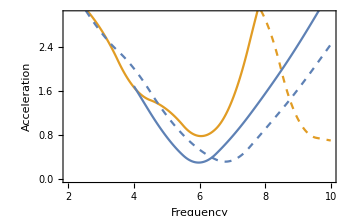
a_s=0 | a_s=0.03
-Graphics- | -Graphics-

```mathematica
p=Legended[Grid[{{Style[DisplayForm[RowBox[{Subscript[a,s],"=","0"}]],16],Style[DisplayForm[RowBox[{Subscript[a,s],"=","0.03"}]],16]},{p0,p1}}],LineLegend[{Directive[ColorData[97,"ColorList"][[1]]],Directive[ColorData[97,"ColorList"][[1]],Dashed],Directive[ColorData[97,"ColorList"][[2]]],Directive[ColorData[97,"ColorList"][[2]],Dashed]},{"Subharmonic k=0.95π","Subharmonic k=1.05π","Harmonic k=1.9π","Harmonic k=2.1π"}]]
```

```mathematica
Export["boundaries.pdf",p]
```

boundaries.pdf